# 2 Dimensions

First, define the numerics to have some feduciary point

```mathematica
(*Check that the analytics match numerics that mathematica gives*)
```

```mathematica
NIntegrate[NIntegrate[Conjugate[Ψ[1,x,1,y,10]]*H2p[2,x,2,y,10,Ψ,1.5,1,1],{x,-10/2,10/2}],{y,-10/2,10/2}]//Chop//Quiet
```

-0.0345411

```mathematica
H2Plane[1.5,10,1,1,1,2,2]
```

-0.0345411+0. ⅈ

```mathematica
(*They match up, which is a good sign*)

(*Now look at
```

```mathematica
NIntegrate[NIntegrate[Conjugate[Ψ[2,x,2,y,10]]*Hp[1,x,1,y,10,Ψ,1.5,1,-1],{x,-10/2,10/2}],{y,-10/2,10/2}]//Chop//Quiet
```

-0.0172705+0.0125478 ⅈ

```mathematica
HPlanebtest[1.5,10,2,2,1,1,-1]
```

-0.0172705+0.0125478 ⅈ

```mathematica
(*When I was using flatten, I had to know what flatten would do. Here is how table arranges various indices*)
```

```mathematica
TestMatrix = Table[x1*y1*x2*y2,{x1,{m1,m2}},{y1,{n1,n2}},{x2,{l1,l2}},{y2,{q1,q2}}]//MatrixForm
```

((l1 m1 n1 q1 | l1 m1 n1 q2
l2 m1 n1 q1 | l2 m1 n1 q2) | (l1 m1 n2 q1 | l1 m1 n2 q2
l2 m1 n2 q1 | l2 m1 n2 q2)
(l1 m2 n1 q1 | l1 m2 n1 q2
l2 m2 n1 q1 | l2 m2 n1 q2) | (l1 m2 n2 q1 | l1 m2 n2 q2
l2 m2 n2 q1 | l2 m2 n2 q2))

```mathematica
(*Summary of testing: I have confirmed that for random matrix elements, my function for one well with an offset gives the same matrix element as the equivalent numerical calculation. The two well case is a simple generalization, but I should look at that*)
```

## Sparse Matrices:

```mathematica
(*Summary of testing: I have built new modules that calculate the matrices much quicker. There is still work to be done to speed them up more, but I have to think a little more carefully about this, I am going to start using them to investigate the behaviour of the 2D-1Well case, to see if the increased resolution solves some of my problems.*)
```

```mathematica
(*First, build a matrix in 2d-well, and look at the energy spectrum and the wavefunction*)
```

```mathematica
H2d1Well = BuildPlaneMatrix[10,5,35];
```

```mathematica
MatrixPlot[N[H2d1Well,8]]
```

-Graphics-

```mathematica
Length[H2d1Well]
```

1225

```mathematica
Energy2d1Well = Eigensystem[N[H2d1Well,8]-1000.*IdentityMatrix[1225],3];
```

```mathematica
(*The diagonalization is starting to become non-trivial and overwhelm the actual construction of the matrices*)
```

```mathematica
(*Now, visualize the ground state, and the excited state)
```

```mathematica
Energy2d1Well[[1]][[3]]+1000
```

-0.771264-1.06581×10^-13 ⅈ

```mathematica
groundState[Energy2d1Well[[2]][[1]],5,1,1]
```

0.264313-0.192035 ⅈ

```mathematica
Plot3D[Abs[groundState[Energy2d1Well[[2]][[1]],5,x,y]]^2,{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[Abs[groundState[Energy2d1Well[[2]][[2]],5,x,y]]^2,{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[Abs[groundState[Energy2d1Well[[2]][[3]],5,x,y]]^2,{x,-2,2},{y,-2,2}]
```

$Aborted

```mathematica
(*I think what is happening is that I am getting aliasing. So, to calculate the tunneling rates, we need to be confident about the second excited state as well. To help, I am going to increase the depth of the well, and increase the length of the box. The smallest resolution with a length of L will be k=2 π/D=2 π/L n D = L/35 =.3 This will be a problem when we are looking at interwell seperations of less than .3.
```

```mathematica
H2d1WellL10 = BuildPlaneMatrix[4,10,35];
```

```mathematica
MatrixPlot[N[H2d1Well,8]]
```

-Graphics-

```mathematica
Length[H2d1Well]
```

1225

```mathematica
Energy2d1Well = Eigensystem[N[H2d1Well,8]-1000.*IdentityMatrix[1225],3];
```

```mathematica
(*The diagonalization is starting to become non-trivial and overwhelm the actual construction of the matrices*)
```

```mathematica
(*Now, visualize the ground state, and the excited state)
```

```mathematica
Energy2d1Well[[1]][[2]]+1000
```

0.593527+6.13503×10^-15 ⅈ

```mathematica
groundState[Energy2d1Well[[2]][[1]],5,1,1]
```

0.113751-8.86668×10^-13 ⅈ

```mathematica
Plot3D[Abs[groundState[Energy2d1Well[[2]][[1]],10,x,y]]^2,{x,-2,2},{y,-2,2},PlotRange->{0,.4}]
```

-Graphics3D-

```mathematica
Plot3D[Abs[groundState[Energy2d1Well[[2]][[2]],10,x,y]]^2,{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
Plot3D[{Re[groundState[Energy2d1Well[[2]][[2]],10,x,y]],Im[groundState[Energy2d1Well[[2]][[2]],10,x,y]]},{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
Log[10^-8]
```

-Log[100000000]

```mathematica
(*Let's examine, quantitaviely, if the energy looks like it is converging*)
```

```mathematica
(*Look at the first energy state*)
```

```mathematica
(* Something that would be useful is to see how these things scale as a value of the length scale. Fix # at 35 and see how the things converge as L is changed.*)
```

```mathematica
Energy2D1WellLConvergep30 = Table[{L,Eigenvalues[ BuildPlaneMatrix[10,L,30]-1000*IdentityMatrix[30^2],1][[1]]+1000},{L,2,15,2}]
```

{{2,2071.18},{4,-4.71509+6.55791×10^-15 ⅈ},{6,-4.71562},{8,-4.71562},{10,-4.71559},{12,-4.71497},{14,-4.71106}}

```mathematica
Energy2D1WellLConvergep30 = Table[{L,Eigenvalues[ BuildPlaneMatrix[10,L,30]-1000*IdentityMatrix[30^2],2][[2]]+1000},{L,2,15,2}]
```

{{2,2071.18},{4,-0.8165-8.15985×10^-14 ⅈ},{6,-0.784953},{8,-0.782587},{10,-0.782364},{12,-0.781503},{14,-0.776486}}

```mathematica
EnergyConver2D1E = Table[{p,Eigenvalues[BuildPlaneMatrix[2,5,p]-1000.*IdentityMatrix[p^2],1]},{p,10,35,4}]
```

{{10,{-1000.17}},{14,{-1000.17}},{18,{-1000.17+2.38426×10^-16 ⅈ}},{22,{-1000.17}},{26,{-1000.17}},{30,{-1000.17+8.92325×10^-14 ⅈ}},{34,{-1000.17}}}

```mathematica
EnergyConver2D1EG = Table[{EnergyConver2D1E[[p]][[1]],Abs[Log10[EnergyConver2D1E[[p+1]][[2]][[1]]-EnergyConver2D1E[[p]][[2]]]][[1]]},{p,1,6}]
```

{{10,5.05787},{14,7.69346},{18,10.6011},{22,10.9998},{26,11.6652},{30,11.9885}}

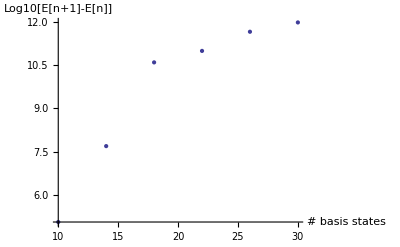

```mathematica
ListPlot[EnergyConver2D1EG,AxesLabel->{"# basis states","Log10[E[n+1]-E[n]]"}]
```

```mathematica
(*Now, look at how this behaves for the second energy. Remeber, we might be having trouble with the aliasing.*)

EnergyConver2D2E = Table[{p,Eigenvalues[BuildPlaneMatrix[2,5,p]-1000.*IdentityMatrix[p^2],2][[2]]+1000},{p,10,35,4}]
```

{{10,0.343993},{14,0.343991},{18,0.343991+1.76398×10^-19 ⅈ},{22,0.343991},{26,0.343991},{30,0.343991+1.79756×10^-13 ⅈ},{34,0.343991}}

```mathematica
EnergyConver2D2EG = Table[{EnergyConver2D1E[[p]][[1]],Abs[Log10[EnergyConver2D1E[[p+1]][[2]][[1]]-EnergyConver2D1E[[p]][[2]]]][[1]]},{p,1,6}]
```

{{10,5.05787},{14,7.69346},{18,10.6011},{22,10.9998},{26,11.6652},{30,11.9885}}

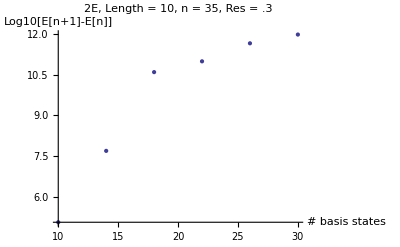

```mathematica
ListPlot[EnergyConver2D2EG,AxesLabel->{"# basis states","Log10[E[n+1]-E[n]]"},PlotLabel->"2E, Length = 10, n = 35, Res = .3"]
```

```mathematica
(*They seem to be converging, but, a more rigorous analysis that takes into account the sizing L must be preformed. *)

(*However, let's see if we can try this for the 2 well case. Note, we need to have a working precision of much higher than .3, if we are looking at interwell seperations on the order of .1. Working with n = 45, L must be 4.5. We will definitely be getting aliasing affects in the second excited state, but I can see how it converges as well.
```

```mathematica
(*BuildPlaneMatrix2D2Well[V_,L_,p_,b_]*)
```

```mathematica
H2d2WellL4d5 = BuildPlaneMatrix2D2Well[3,4.5,45,.1]
```

SparseArray[<4100625>,{2025,2025}]

```mathematica
H2d2WellL5p35bd4 = BuildPlaneMatrix2D2Well[3,5,35,.4]
```

SparseArray[<1500625>,{1225,1225}]

```mathematica
EnergyConver2D2E = Table[{p,Eigenvalues[BuildPlaneMatrix2D2Well[3,5,p,.3]-1000.*IdentityMatrix[p^2],2][[1]]+1000},{p,10,35,4}]
```

{{10,-1.81036},{14,-1.81075},{18,-1.81075},{22,-1.81075},{26,-1.81075+5.87751×10^-24 ⅈ},{30,-1.81075},{34,-1.81075}}

```mathematica
BuildPlaneMatrix2D2Well[3,5,1,.3]
```

SparseArray[<1>,{1,1}]

```mathematica
EnergyConver2D2E = Table[{p,Eigenvalues[BuildPlaneMatrix2D2Well[3,5,p,.3]-1000.*IdentityMatrix[p^2],2][[1]]+1000},{p,10,35,4}]
```

```mathematica
Tunneling2D2 = Table[{b,Eigenvalues[BuildPlaneMatrix2D2Well[10,5,20,b]-1000.*IdentityMatrix[20^2],2]+1000},{b,.5,3,.5}]
```

{{0.5,{-7.72266,-4.69181}},{1.,{-4.83583,-4.66575}},{1.5,{-4.83583,-4.66575}},{2.,{-7.72266,-4.69181}},{2.5,{-12.0845-1.00495×10^-22 ⅈ,-5.36945+3.72917×10^-27 ⅈ}},{3.,{-7.72266,-4.69181}}}

```mathematica
(*Let's calculate some tunneling rates*)
Tunneling2DL8z = Table[{b,Eigenvalues[BuildPlaneMatrix2D2Well[10,8,15,b]-1000.*IdentityMatrix[15^2],2]+1000},{b,.1,3,.1}]
```

{{0.1,{-11.7202,-5.06594}},{0.2,{-11.0722,-5.0013}},{0.3,{-10.0914,-4.90253}},{0.4,{-8.91284,-4.78589}},{0.5,{-7.70026,-4.67607}},{0.6,{-6.61961,-4.59996}},{0.7,{-5.79609,-4.57315}},{0.8,{-5.26335,-4.58869}},{0.9,{-4.965,-4.62218}},{1.,{-4.81849,-4.65044}},{1.1,{-4.7564,-4.66575}},{1.2,{-4.7312,-4.67453}},{1.3,{-4.71594,-4.68461}},{1.4,{-4.70361,-4.69533}},{1.5,{-4.70051,-4.69786}},{1.6,{-4.69997,-4.6982}},{1.7,{-4.70394,-4.69416}},{1.8,{-4.70307,-4.69503}},{1.9,{-4.70025,-4.69785}},{2.,{-4.70327,-4.69481}},{2.1,{-4.70025,-4.69785}},{2.2,{-4.70307,-4.69503}},{2.3,{-4.70394,-4.69416}},{2.4,{-4.69997,-4.6982}},{2.5,{-4.70051,-4.69786}},{2.6,{-4.70361,-4.69533}},{2.7,{-4.71594,-4.68461}},{2.8,{-4.7312,-4.67453}},{2.9,{-4.7564,-4.66575}},{3.,{-4.81849,-4.65044}}}

```mathematica
E1Interwell = Table[{Tunneling2D[[p]][[1]],Tunneling2D[[p]][[2]][[1]]},{p,6}]
```

{{0.5,-7.72261},{0.6,-6.63732},{0.7,-5.80815},{0.8,-5.27384},{0.9,-4.98213},{1.,-4.84127}}

```mathematica
E2Interwell = Table[{Tunneling2D[[p]][[1]],Tunneling2D[[p]][[2]][[2]]},{p,6}]
```

{{0.5,-4.69139},{0.6,-4.61852},{0.7,-4.59774},{0.8,-4.60955},{0.9,-4.63426},{1.,-4.65853}}

```mathematica
EnDifList= Table[{Tunneling2D[[p]][[1]],Tunneling2D[[p]][[2]][[2]]-Tunneling2D[[p]][[2]][[1]]},{p,1,Length[Tunneling2DL8z]}]
```

{{0.1,6.52853},{0.2,5.98576},{0.3,5.15071},{0.4,4.12284},{0.5,3.03122},{0.6,2.01879},{0.7,1.21041},{0.8,0.664289},{0.9,0.347871},{1.,0.182745},{1.1,0.102848},{1.2,0.0706457},{1.3,0.0706457},{1.4,0.102848},{1.5,0.182745},{1.6,0.347871},{1.7,0.664289},{1.8,1.21041},{1.9,2.01879},{2.,3.03122},{2.1,4.12284},{2.2,5.15071},{2.3,5.98576},{2.4,6.52853},{2.5,6.71656},{2.6,6.52853},{2.7,5.98576},{2.8,5.15071},{2.9,4.12284},{3.,3.03122}}

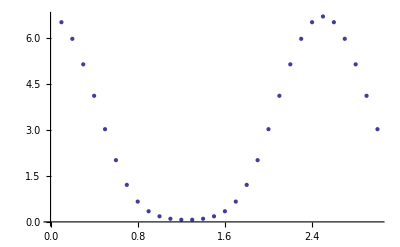

```mathematica
ListPlot[EnDifList]
```

```mathematica
Tunneling2DL10z = Table[{b,Eigenvalues[BuildPlaneMatrix2D2Well[10,8,15,b]-1000.*IdentityMatrix[15^2],2]+1000},{b,.1,2,.1}]
```

{{0.1,{-11.7202,-5.06594}},{0.2,{-11.0722,-5.0013}},{0.3,{-10.0914,-4.90253}},{0.4,{-8.91284,-4.78589}},{0.5,{-7.70026,-4.67607}},{0.6,{-6.61961,-4.59996}},{0.7,{-5.79609,-4.57315}},{0.8,{-5.26335,-4.58869}},{0.9,{-4.965,-4.62218}},{1.,{-4.81849,-4.65044}},{1.1,{-4.7564,-4.66575}},{1.2,{-4.7312,-4.67453}},{1.3,{-4.71594,-4.68461}},{1.4,{-4.70361,-4.69533}},{1.5,{-4.70051,-4.69786}},{1.6,{-4.69997,-4.6982}},{1.7,{-4.70394,-4.69416}},{1.8,{-4.70307,-4.69503}},{1.9,{-4.70025,-4.69785}},{2.,{-4.70327,-4.69481}}}

```mathematica
EnDifListL10= Table[{Tunneling2DL10z[[p]][[1]],Tunneling2DL10z[[p]][[2]][[2]]-Tunneling2DL10z[[p]][[2]][[1]]},{p,1,Length[Tunneling2DL10z]}]
```

{{0.1,6.65426},{0.2,6.07088},{0.3,5.18883},{0.4,4.12695},{0.5,3.0242},{0.6,2.01965},{0.7,1.22294},{0.8,0.674655},{0.9,0.342821},{1.,0.168047},{1.1,0.0906509},{1.2,0.056671},{1.3,0.0313376},{1.4,0.00828102},{1.5,0.00264739},{1.6,0.00177237},{1.7,0.00977975},{1.8,0.00804026},{1.9,0.00239775},{2.,0.00845159}}

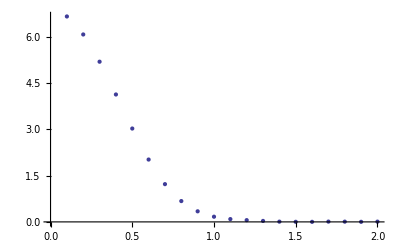

```mathematica
p1=ListPlot[EnDifListL10]
```

```mathematica
NLF1 = NonlinearModelFit[EnDifListL10,A*Exp[-2*x^2/c],{A,c},x]
```

FittedModel[6.98493 ⅇ^(-«19» x^2)]

FittedModel[ⅇ^(-0.544913 x^2)]

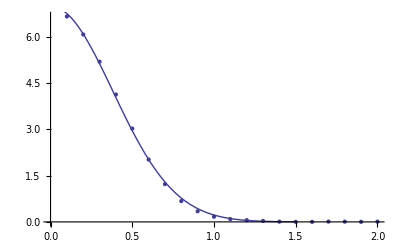

```mathematica
Show[p1,Plot[NLF1[x],{x,0,1.5},Frame-> True]]
```

```mathematica
(*Well, that is nice. Now, compare this to the 1D case*)
```

```mathematica
TunnelingInterwellP=Table[{p,computePlaneMatrix2Well[10,.5,p,8,40][[1]][[2]]-computePlaneMatrix2Well[10,.5,p,8,40][[1]][[1]]},{p,.1,5,.1}]
```

{{0.1,7.14266},{0.2,6.55806},{0.3,5.64945},{0.4,4.51427},{0.5,3.28653},{0.6,2.12954},{0.7,1.20642},{0.8,0.606203},{0.9,0.284652},{1.,0.131098},{1.1,0.0604755},{1.2,0.0280532},{1.3,0.0130684},{1.4,0.00610253},{1.5,0.0028537},{1.6,0.00133695},{1.7,0.000630452},{1.8,0.000305822},{1.9,0.000166393},{2.,0.000127723},{2.1,0.000166393},{2.2,0.000305822},{2.3,0.000630452},{2.4,0.00133695},{2.5,0.0028537},{2.6,0.00610253},{2.7,0.0130684},{2.8,0.0280532},{2.9,0.0604755},{3.,0.131098},{3.1,0.284652},{3.2,0.606203},{3.3,1.20642},{3.4,2.12954},{3.5,3.28653},{3.6,4.51427},{3.7,5.64945},{3.8,6.55806},{3.9,7.14266},{4.,7.34414},{4.1,7.14266},{4.2,6.55806},{4.3,5.64945},{4.4,4.51427},{4.5,3.28653},{4.6,2.12954},{4.7,1.20642},{4.8,0.606203},{4.9,0.284652},{5.,0.131098}}

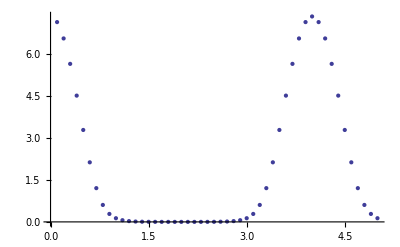

```mathematica
p2=ListPlot[TunnelingInterwellP]
```

```mathematica
NLF2 = NonlinearModelFit[TunnelingInterwellP,A*Exp[-2*x^2/c],{A,c},x]
```

FittedModel[7.59071 ⅇ^(-«19» x^2)]

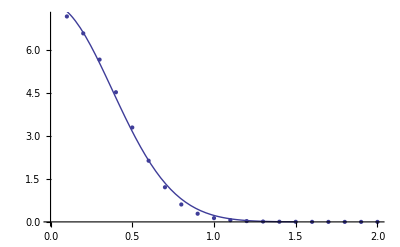

```mathematica
Show[p2,Plot[NLF2[x],{x,0,1.5},Frame-> True]]
```

```mathematica
NLF2[.2]
```

6.5935

7.59071 ⅇ^(-3.52104 x^2)

```mathematica
EnDif[b_] :=Module[{E,E1,E2}, 
E= Eigenvalues[BuildPlaneMatrix2D2Well[10,5,10,b]-1000.*IdentityMatrix[100],2];
E1 = E[[1]];E2 = E[[2]];
E1-E2]
```

```mathematica
(*This looks weird. Let's construct the wigner functions first, and see if we can visualize what they are doing as the b gets bigger*)
```

```mathematica
(*First, construct a single wigner function*)
```

```mathematica
WigMatrix = BuildPlaneMatrix2D2Well[10,7,20,1]
```

SparseArray[<160000>,{400,400}]

SparseArray[<160000>,{400,400}]

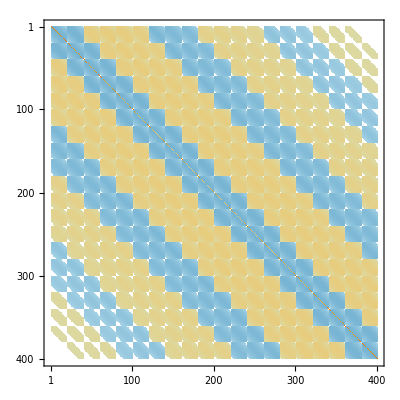

```mathematica
MatrixPlot[WigMatrix]
```

```mathematica
WigEVectors = Eigensystem[WigMatrix-1000.*IdentityMatrix[20^2],2]
```

```mathematica
WigEVectors[[2]][[1]]
```

```mathematica
WigPsi0 [x_,y_] = groundState[WigEVectors[[2]][[1]],7,x,y]
```

```mathematica
WigPsi1[x_,y_] = groundState[WigEVectors[[2]][[2]],7,x,y]
```

```mathematica
Plot3D[Re[WigPsi0[x,y]],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[Im[WigPsi1[x,y]],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
(*Yay! Now, build the wig functions!*)
```

```mathematica
Wig1 [x_,y_] =(Re[WigPsi0[x,y]]+Im[WigPsi1[x,y]])/Sqrt[2];
```

```mathematica
Wig2 [x_,y_] =(Re[WigPsi0[x,y]]-Im[WigPsi1[x,y]])/Sqrt[2];
```

```mathematica
Wig1[0,0]
```

(Im[WigPsi1]+Re[WigPsi0])/(√2)

```mathematica
p2=Plot3D[Wig1[x,y],{x,-2,2},{y,-2,2},PlotRange->{0,1}]
```

-Graphics3D-

```mathematica
p1=Plot3D[Wig2[x,y],{x,-2,2},{y,-2,2},PlotRange->{0,1},PlotStyle->Red]
```

-Graphics3D-

```mathematica
Show[p1,p2]
```

-Graphics3D-

```mathematica
(*Kaden had some interest in seeing how the tunneling rates behave at large distances, as from WKB we expect a Exp[-] behaviour for tunneling. *)
```

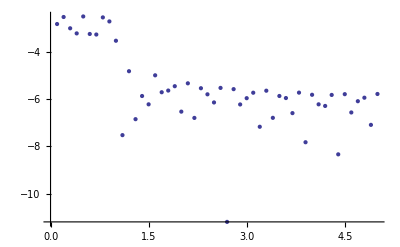

```mathematica
LargeTunnelEr = ListPlot[Table[{p/10.,Log[Abs[TunnelingInterwellP[[p]][[2]]-NLF2[p/10.]]]},{p,1,50}]]
```

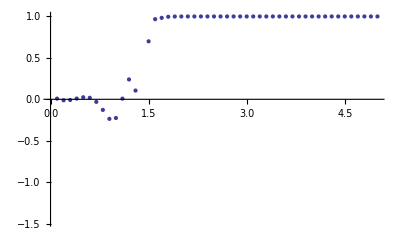

```mathematica
LargeTunnelEr = ListPlot[Table[{p/10.,(TunnelingInterwellP[[p]][[2]]-NLF2[p/10.])/(TunnelingInterwellP[[p]][[2]])},{p,1,50}]]
```

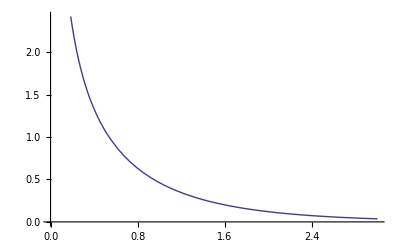

```mathematica
Plot[BesselK[1/2,x],{x,0,3}]
```

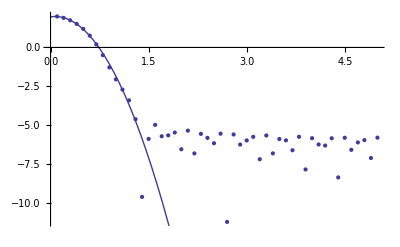

```mathematica
Show[ ListPlot[Table[{p/10.,Log[TunnelingInterwellP[[p]][[2]]]},{p,1,50}]],Plot[Log[NLF2[x]],{x,0,4}]]
```

```mathematica
(*We may be getting aliasing from the box length. Try increasing the box length to 20 to see if that helps.*)
```

```mathematica
TunnelingInterwellPL14=Table[{p,computePlaneMatrix2Well[10,.5,p,14,45][[1]][[2]]-computePlaneMatrix2Well[10,.5,p,14,45][[1]][[1]]},{p,.1,5,.1}]
```

{{0.1,7.14336},{0.2,6.55834},{0.3,5.64948},{0.4,4.51427},{0.5,3.28654},{0.6,2.12954},{0.7,1.20643},{0.8,0.606207},{0.9,0.284646},{1.,0.131107},{1.1,0.0604755},{1.2,0.0280463},{1.3,0.0130754},{1.4,0.00610119},{1.5,0.00284632},{1.6,0.00134044},{1.7,0.000623113},{1.8,0.000286503},{1.9,0.000142496},{2.,0.0000631016},{2.1,0.0000249438},{2.2,0.0000194898},{2.3,5.89184×10^-6},{2.4,1.60826×10^-6},{2.5,6.58445×10^-6},{2.6,1.71221×10^-7},{2.7,4.20241×10^-6},{2.8,5.02321×10^-6},{2.9,2.68064×10^-7},{3.,4.42002×10^-6},{3.1,4.68792×10^-6},{3.2,1.62365×10^-7},{3.3,4.45803×10^-6},{3.4,4.53655×10^-6},{3.5,1.81899×10^-12},{3.6,4.53654×10^-6},{3.7,4.45806×10^-6},{3.8,1.62374×10^-7},{3.9,4.68793×10^-6},{4.,4.42×10^-6},{4.1,2.68079×10^-7},{4.2,5.02319×10^-6},{4.3,4.20243×10^-6},{4.4,1.71205×10^-7},{4.5,6.58435×10^-6},{4.6,1.60825×10^-6},{4.7,5.8919×10^-6},{4.8,0.0000194898},{4.9,0.0000249438},{5.,0.0000631016}}

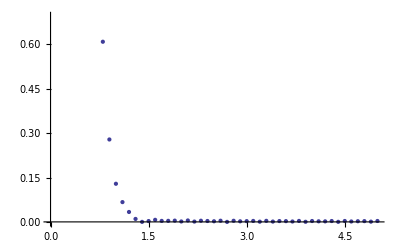

```mathematica
ListPlot[TunnelingInterwellP]
```

```mathematica
Show[ ListPlot[Table[{p/10.,Log[TunnelingInterwellP[[p]][[2]]]},{p,1,50}]],Plot[Log[NLF2[x]],{x,0,4}]]
```

-Graphics-

```mathematica
NLF3 = NonlinearModelFit[TunnelingInterwellPL14,A*Exp[-2*x^2/c]+B*Exp[-d*x],{A,c,B,d},x]
```

FittedModel[-2.46113 ⅇ^(-«17» x)+9.24117 «1»]

```mathematica
NLF3[x]
```

-2.46113 ⅇ^(-3.02892 x)+9.24117 ⅇ^(-3.61901 x^2)

```mathematica
NLF3[2]
```

-0.00575291

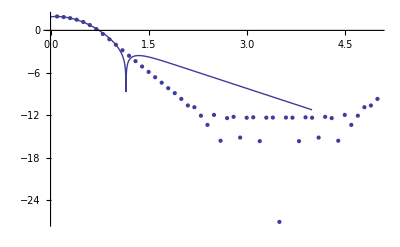

```mathematica
Show[ ListPlot[Table[{p/10.,Log[TunnelingInterwellPL14[[p]][[2]]]},{p,1,50}]],Plot[Log[Abs[NLF3[x]]],{x,0,4}]]
```

```mathematica
TunnelingInterwellPL12=Table[{p,computePlaneMatrix2Well[10,.5,p,12,50][[1]][[2]]-computePlaneMatrix2Well[10,.5,p,12,50][[1]][[1]]},{p,.1,5,.1}]
```

{{0.1,7.14266},{0.2,6.55806},{0.3,5.64945},{0.4,4.51427},{0.5,3.28653},{0.6,2.12954},{0.7,1.20642},{0.8,0.606203},{0.9,0.284652},{1.,0.131098},{1.1,0.0604754},{1.2,0.028053},{1.3,0.0130681},{1.4,0.00610185},{1.5,0.00285229},{1.6,0.00133388},{1.7,0.000623927},{1.8,0.000291841},{1.9,0.000136522},{2.,0.0000638653},{2.1,0.0000298647},{2.2,0.0000139858},{2.3,6.52464×10^-6},{2.4,3.069×10^-6},{2.5,1.42386×10^-6},{2.6,6.73099×10^-7},{2.7,3.19118×10^-7},{2.8,1.45936×10^-7},{2.9,9.41782×10^-8},{3.,5.22687×10^-8},{3.1,9.41418×10^-8},{3.2,1.45939×10^-7},{3.3,3.19118×10^-7},{3.4,6.73061×10^-7},{3.5,1.42377×10^-6},{3.6,3.06906×10^-6},{3.7,6.52462×10^-6},{3.8,0.0000139858},{3.9,0.0000298647},{4.,0.0000638653},{4.1,0.000136522},{4.2,0.000291841},{4.3,0.000623927},{4.4,0.00133388},{4.5,0.00285229},{4.6,0.00610185},{4.7,0.0130681},{4.8,0.028053},{4.9,0.0604754},{5.,0.131098}}

```mathematica
Show[ ListPlot[Table[{p/10.,Log[TunnelingInterwellPL12[[p]][[2]]]},{p,1,50}]],Plot[Log[Abs[NLF4[x]]],{x,0,4}]]
```

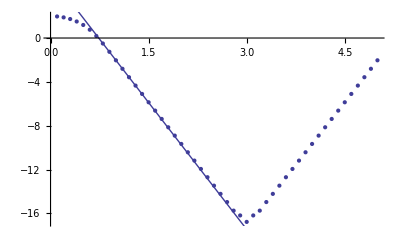

```mathematica
NLF4 = NonlinearModelFit[TunnelingInterwellPL12[[10;;30]],B*Exp[-d*x],{A,c,B,d},x]
```

FittedModel[292.283 ⅇ^(-«18» x)]

```mathematica
NLF5[x]
```

265.219 ⅇ^(-7.62863 x)

```mathematica
(*Okay, so I have verified that at the beginning it looks like a gaussian, and then it trails off like an exponential. I want to see the convergence on these energy values though, as the box size is making every thing suspicious (ie. the next well over is starting to interact with the tunneling rates*)
```

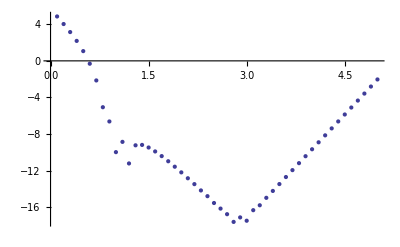

```mathematica
p5= ListPlot[Table[{p/10.,Log[Abs[TunnelingInterwellPL12[[p]][[2]]-NLF4[p/10.]]]},{p,1,50}]]
```

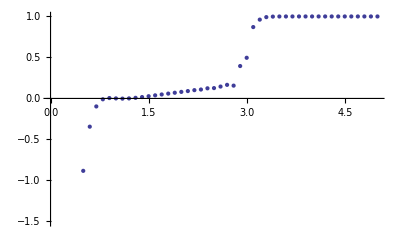

```mathematica
p5= ListPlot[Table[{p/10.,(TunnelingInterwellPL12[[p]][[2]]-NLF4[p/10.])/(TunnelingInterwellPL12[[p]][[2]])},{p,1,50}]]
```

```mathematica
25/200.
```

0.125

```mathematica
TunnelingInterwellPL25p80=Table[{p,computePlaneMatrix2Well[10,.5,p,25,130][[1]][[2]]-computePlaneMatrix2Well[10,.5,p,25,130][[1]][[1]]},{p,.1,5,.1}]
```

{{0.1,7.14266},{0.2,6.55806},{0.3,5.64945},{0.4,4.51427},{0.5,3.28653},{0.6,2.12954},{0.7,1.20642},{0.8,0.606203},{0.9,0.284652},{1.,0.131098},{1.1,0.0604754},{1.2,0.028053},{1.3,0.0130681},{1.4,0.00610186},{1.5,0.00285227},{1.6,0.00133389},{1.7,0.000623915},{1.8,0.000291848},{1.9,0.00013652},{2.,0.0000638616},{2.1,0.0000298733},{2.2,0.0000139742},{2.3,6.53687×10^-6},{2.4,3.05788×10^-6},{2.5,1.43047×10^-6},{2.6,6.69133×10^-7},{2.7,3.13039×10^-7},{2.8,1.46401×10^-7},{2.9,6.8485×10^-8},{3.,3.20197×10^-8},{3.1,1.50212×10^-8},{3.2,7.07041×10^-9},{3.3,3.27236×10^-9},{3.4,1.54978×10^-9},{3.5,7.53062×10^-10},{3.6,3.7835×10^-10},{3.7,1.63709×10^-10},{3.8,8.36735×10^-11},{3.9,4.91127×10^-11},{4.,2.00089×10^-11},{4.1,2.36469×10^-11},{4.2,1.01863×10^-10},{4.3,1.81899×10^-11},{4.4,2.18279×10^-11},{4.5,4.36557×10^-11},{4.6,9.45874×10^-11},{4.7,8.91305×10^-11},{4.8,3.63798×10^-12},{4.9,1.81899×10^-11},{5.,1.27329×10^-10}}

FittedModel[265.219 ⅇ^(-«18» x)]

```mathematica
NLF4 = NonlinearModelFit[TunnelingInterwellPL25p80[[20;;]],B*Exp[-d*x],{B,d},x]
```

FittedModel[291.155 ⅇ^(-«18»«1»«1»)]

```mathematica
NLF4[x]
```

291.155 ⅇ^(-3.85329 x)

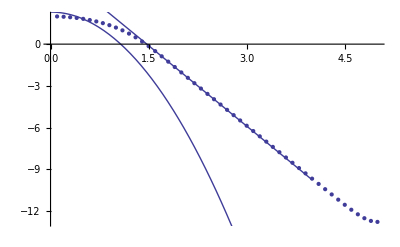

```mathematica
Show[ ListPlot[Table[{p/10.,Log[TunnelingInterwellPL25p80[[p]][[2]]]},{p,1,50}]],Plot[Log[Abs[NLF4[x]]],{x,0,4}],{x,0,4}]]
```

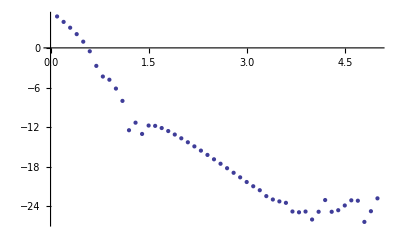

```mathematica
p6= ListPlot[Table[{p/10.,Log[Abs[TunnelingInterwellPL25p80[[p]][[2]]-NLF5[p/10.]]]},{p,1,50}]]
```

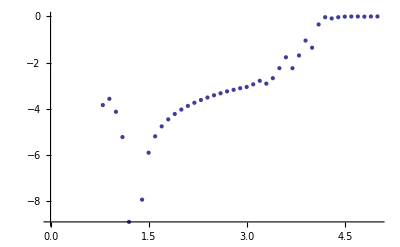

```mathematica
p7= ListPlot[Table[{p/10.,Log[(TunnelingInterwellPL25p80[[p]][[2]]-NLF5[p/10.])/(TunnelingInterwellPL25p80[[p]][[2]])]},{p,1,50}]]
```

```mathematica
TunnelingInterwellPVarp80=Table[{p,computePlaneMatrix2Well[10,.5,p,4.+p*4.,80][[1]][[2]]-computePlaneMatrix2Well[10,.5,p,4.+p*4.,80][[1]][[1]]},{p,.1,5,.1}]
```

{{0.1,7.14269},{0.2,6.55807},{0.3,5.64945},{0.4,4.51427},{0.5,3.28653},{0.6,2.12954},{0.7,1.20642},{0.8,0.606203},{0.9,0.284652},{1.,0.131098},{1.1,0.0604754},{1.2,0.028053},{1.3,0.0130681},{1.4,0.00610186},{1.5,0.00285228},{1.6,0.00133389},{1.7,0.000623915},{1.8,0.000291848},{1.9,0.00013652},{2.,0.0000638615},{2.1,0.0000298733},{2.2,0.0000139742},{2.3,6.53688×10^-6},{2.4,3.05782×10^-6},{2.5,1.4304×10^-6},{2.6,6.69139×10^-7},{2.7,3.13028×10^-7},{2.8,1.46403×10^-7},{2.9,6.85177×10^-8},{3.,3.20924×10^-8},{3.1,1.50776×10^-8},{3.2,7.14499×10^-9},{3.3,3.2669×10^-9},{3.4,9.74978×10^-10},{3.5,8.56744×10^-10},{3.6,2.41744×10^-9},{3.7,2.5957×10^-9},{3.8,8.94943×10^-10},{3.9,1.07593×10^-8},{4.,2.84672×10^-8},{4.1,5.13901×10^-8},{4.2,7.03403×10^-8},{4.3,6.75227×10^-8},{4.4,1.81262×10^-8},{4.5,1.04492×10^-7},{4.6,3.18607×10^-7},{4.7,6.21605×10^-7},{4.8,9.7569×10^-7},{4.9,1.29865×10^-6},{5.,1.45984×10^-6}}

```mathematica
4/80//N
```

0.05

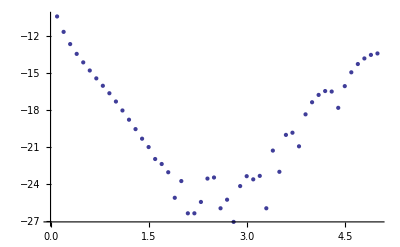

```mathematica
p9= ListPlot[Table[{p/10.,Log[Abs[TunnelingInterwellPL25p80[[p]][[2]]-TunnelingInterwellPVarp80[[p]][[2]] ] ]},{p,1,50}]]
```

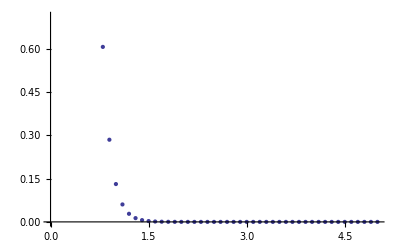

```mathematica
p10= ListPlot[Table[{p/10.,Abs[TunnelingInterwellPL25p80[[p]][[2]]]},{p,1,50}]]
```

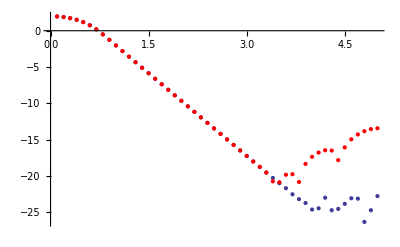

```mathematica
Show[ ListPlot[Table[{p/10.,Log[Abs[TunnelingInterwellPL25p80[[p]][[2]]]]},{p,1,50}]],ListPlot[Table[{p/10.,Log[Abs[TunnelingInterwellPVarp80[[p]][[2]] ]]},{p,1,50}],PlotStyle->Red]]
```

```mathematica
(*The variable box length seems to actually work very well! Let's test that we aren't just getting a false positive though. Plot this with really shitty resolution and make sure that the plots don't match up
```

```mathematica
TunnelingInterwellPVarp80Bad=Table[{p,computePlaneMatrix2Well[10,.5,p,100.*Exp[-p]+1.2*p,80][[1]][[2]]-computePlaneMatrix2Well[10,.5,p,100.*Exp[-p]+1.2*p,80][[1]][[1]]},{p,.1,5,.1}]
```

{{0.1,9.35763},{0.2,8.41344},{0.3,6.97055},{0.4,5.24382},{0.5,3.53188},{0.6,2.13553},{0.7,1.21986},{0.8,0.641995},{0.9,0.278523},{1.,0.132099},{1.1,0.060953},{1.2,0.027989},{1.3,0.0130262},{1.4,0.00612772},{1.5,0.00285083},{1.6,0.00133324},{1.7,0.000623842},{1.8,0.000291841},{1.9,0.00013652},{2.,0.0000638616},{2.1,0.0000298732},{2.2,0.0000139742},{2.3,6.53682×10^-6},{2.4,3.0582×10^-6},{2.5,1.44491×10^-6},{2.6,1.0514×10^-6},{2.7,7.90664×10^-6},{2.8,0.000116974},{2.9,0.00142663},{3.,0.0141734},{3.1,0.119018},{3.2,0.818302},{3.3,2.99397},{3.4,5.55839},{3.5,7.10134},{3.6,7.23395},{3.7,6.19487},{3.8,4.49662},{3.9,2.7128},{4.,1.33141},{4.1,0.55757},{4.2,0.225328},{4.3,0.0949909},{4.4,0.0424308},{4.5,0.0200114},{4.6,0.00993918},{4.7,0.00523624},{4.8,0.00300566},{4.9,0.0019822},{5.,0.00158717}}

```mathematica
20/80//N
```

0.25

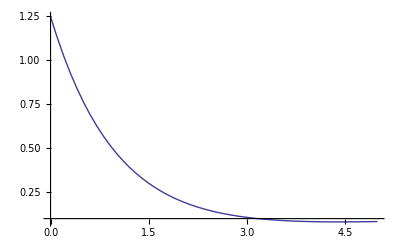

```mathematica
Plot[{(100*Exp[-x]+1.2*x)/80},{x,0,5}]
```

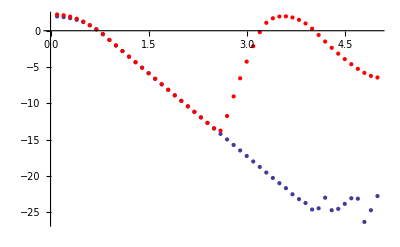

```mathematica
Show[ ListPlot[Table[{p/10.,Log[Abs[TunnelingInterwellPL25p80[[p]][[2]]]]},{p,1,50}]],ListPlot[Table[{p/10.,Log[Abs[TunnelingInterwellPVarp80Bad[[p]][[2]] ]]},{p,1,50}],PlotStyle->Red]]
```

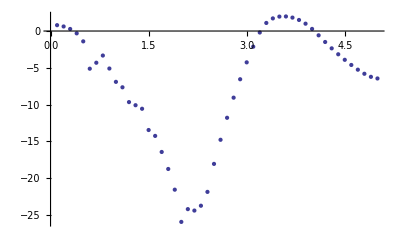

```mathematica
p6= ListPlot[Table[{p/10.,Log[Abs[TunnelingInterwellPVarp80Bad[[p]][[2]]-TunnelingInterwellPL25p80[[p]][[2]]]]},{p,1,50}]]
```

```mathematica
p6= ListPlot[Table[{p/10.,Log[Abs[TunnelingInterwellPVarp80[[p]][[2]]-TunnelingInterwellPL25p80[[p]][[2]]]]},{p,1,50}]]
```

-Graphics-

```mathematica
(*Comparing the two graphs above, the first is the 'shitty' variable, where I choose a variable L that I know is bad, to make sure that my assumption that the resolution depends on L/p is good. It seems that when I choose an intelligent variable scaling, I can get good resolution. Keep in mind that, TunnelingIntwellPL25p80 actually has 120 basis states. So, we can just as good tunneling rates. I am also going to check to make sure that the variable scaling is actually responsible, and not just that more basis states improve the resolution.*)
```

```mathematica
TunnelingInterwellPVarp80TestConstantL=Table[{p,computePlaneMatrix2Well[10,.5,p/2.,25,80][[1]][[2]]-computePlaneMatrix2Well[10,.5,p/2.,25,80][[1]][[1]]},{p,.1,5,.1}]
```

{{0.1,7.29456},{0.2,7.14356},{0.3,6.8961},{0.4,6.55843},{0.5,6.13921},{0.6,5.64949},{0.7,5.10263},{0.8,4.51427},{0.9,3.90229},{1.,3.28654},{1.1,2.68837},{1.2,2.12954},{1.3,1.6303},{1.4,1.20643},{1.5,0.865737},{1.6,0.606211},{1.7,0.417405},{1.8,0.284643},{1.9,0.193276},{2.,0.131107},{2.1,0.0889927},{2.2,0.0604796},{2.3,0.0411551},{2.4,0.0280427},{2.5,0.0191357},{2.6,0.0130748},{2.7,0.00893801},{2.8,0.00610553},{2.9,0.00416554},{3.,0.0028429},{3.1,0.00194682},{3.2,0.00133923},{3.3,0.000921142},{3.4,0.000627719},{3.5,0.000422018},{3.6,0.00028347},{3.7,0.000195684},{3.8,0.000140625},{3.9,0.0001013},{4.,0.0000679254},{4.1,0.0000401489},{4.2,0.0000223754},{4.3,0.0000162325},{4.4,0.0000169557},{4.5,0.0000166495},{4.6,0.000010867},{4.7,2.01265×10^-6},{4.8,3.64325×10^-6},{4.9,2.35929×10^-6},{5.,3.38967×10^-6}}

```mathematica
(*Looking for a shitty resolution at b<1 Res = L/80, = .3, so the points less than .3 should be crappy. Actually, not so, it won't matter as the actual distance is 2*b. So,
```

```mathematica
25/80//N
```

0.3125

```mathematica
TunnelingInterwellPL25p80=Table[{p,computePlaneMatrix2Well[10,.5,p/2.,10,130][[1]][[2]]-computePlaneMatrix2Well[10,.5,p/2.,10,130][[1]][[1]]},{p,.1,5,.1}]
```

{{0.1,7.29346},{0.2,7.14266},{0.3,6.89546},{0.4,6.55806},{0.5,6.13905},{0.6,5.64945},{0.7,5.10262},{0.8,4.51427},{0.9,3.90228},{1.,3.28653},{1.1,2.68837},{1.2,2.12954},{1.3,1.6303},{1.4,1.20642},{1.5,0.865722},{1.6,0.606203},{1.7,0.417409},{1.8,0.284652},{1.9,0.193278},{2.,0.131098},{2.1,0.0889807},{2.2,0.0604754},{2.3,0.0411619},{2.4,0.028053},{2.5,0.0191391},{2.6,0.0130681},{2.7,0.00892792},{2.8,0.00610186},{2.9,0.00417147},{3.,0.00285228},{3.1,0.00195048},{3.2,0.00133389},{3.3,0.00091226},{3.4,0.000623919},{3.5,0.000426721},{3.6,0.000291855},{3.7,0.000199618},{3.8,0.000136535},{3.9,0.0000933942},{4.,0.0000638936},{4.1,0.0000437247},{4.2,0.0000299418},{4.3,0.0000205319},{4.4,0.0000141205},{4.5,9.77165×10^-6},{4.6,6.84986×10^-6},{4.7,4.92855×10^-6},{4.8,3.72692×10^-6},{4.9,3.0697×10^-6},{5.,2.86081×10^-6}}

```mathematica
TunnelingInterwellPVarp80=Table[{p,computePlaneMatrix2Well[10,.5,p/2,4.+p*4.,80][[1]][[2]]-computePlaneMatrix2Well[10,.5,p/2,4.+p*4.,80][[1]][[1]]},{p,.1,5,.1}]
```

{{0.1,7.29348},{0.2,7.14266},{0.3,6.89547},{0.4,6.55806},{0.5,6.13905},{0.6,5.64945},{0.7,5.10262},{0.8,4.51427},{0.9,3.90228},{1.,3.28653},{1.1,2.68837},{1.2,2.12954},{1.3,1.6303},{1.4,1.20642},{1.5,0.865722},{1.6,0.606203},{1.7,0.417409},{1.8,0.284652},{1.9,0.193278},{2.,0.131098},{2.1,0.0889807},{2.2,0.0604754},{2.3,0.0411619},{2.4,0.028053},{2.5,0.0191391},{2.6,0.0130681},{2.7,0.00892792},{2.8,0.00610186},{2.9,0.00417147},{3.,0.00285227},{3.1,0.00195048},{3.2,0.00133389},{3.3,0.000912258},{3.4,0.000623914},{3.5,0.000426714},{3.6,0.000291844},{3.7,0.000199602},{3.8,0.000136515},{3.9,0.0000933704},{4.,0.0000638709},{4.1,0.0000437122},{4.2,0.0000299549},{4.3,0.0000205931},{4.4,0.0000142586},{4.5,0.0000100178},{4.6,7.2314×10^-6},{4.7,5.45496×10^-6},{4.8,4.37094×10^-6},{4.9,3.73841×10^-6},{5.,3.35782×10^-6}}

```mathematica
10/130//N
```

0.0769231

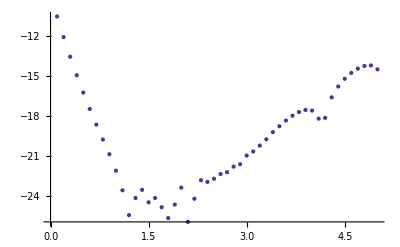

```mathematica
p16= ListPlot[Table[{p/10.,Log[Abs[TunnelingInterwellPVarp80[[p]][[2]]-TunnelingInterwellPL25p80[[p]][[2]]]]},{p,1,50}]]
```

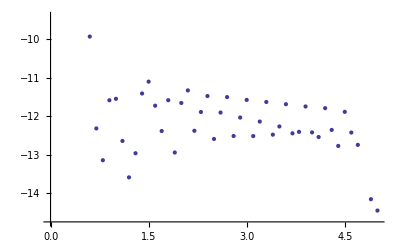

```mathematica
p17 = ListPlot[Table[{p/10.,Log[Abs[TunnelingInterwellPVarp80TestConstantL[[p]][[2]]-TunnelingInterwellPL25p80[[p]][[2]]]]},{p,1,50}]]
```

```mathematica
(*The variable length gets us more information, better, and faster. I will use this going forward in the 2D case.*)

(**************************************************)
```

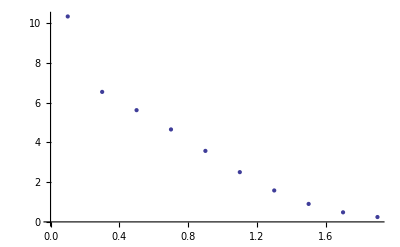

```mathematica
Tun2Dp15lVar=ListPlot[Tunneling2DWellListGen[15]]
```

```mathematica
{Clear[Tunneling2DWellListGen]}
```

{Null}

```mathematica
TunnelingList= Table[{Tun2Dp15lVar[[p]][[1]],Tun2Dp15lVar[[p]][[2]][[2]]-Tun2Dp15lVar[[p]][[2]][[1]]},{p,1,Length[Tun2Dp15lVar]}]
```

{}

```mathematica
Tun2Dp20lVar=Tunneling2DWellListGen[20]
```

{{0.1,2.73483},{0.3,5.80544},{0.5,5.56313},{0.7,4.64972},{0.9,3.57552},{1.1,2.50603},{1.3,1.58281},{1.5,0.903661},{1.7,0.480111},{1.9,0.247732},{2.1,0.129088},{2.3,0.071446},{2.5,0.0460931},{2.7,0.0383001},{2.9,0.0403216},{3.1,0.0478144},{3.3,0.0581673},{3.5,0.06973},{3.7,0.0814389},{3.9,0.0926171}}

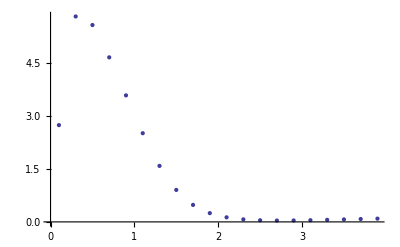

```mathematica
ListPlot[Tun2Dp20lVar]
```

```mathematica
NLF5 = NonlinearModelFit[TunnelingInterwellPL25p80[[12;;30]],B*Exp[-d*x],{A,c,B,d},x]
```

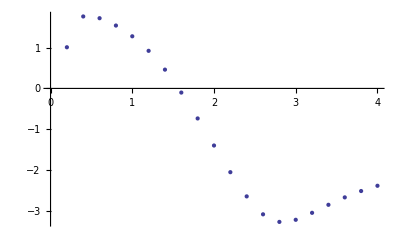

```mathematica
p17 = ListPlot[Table[{p/5.,Log[Abs[Tun2Dp20lVar[[p]][[2]] ]]},{p,1,20}]]
```

```mathematica
Tun2Dp20lVar=Tunneling2DWellListGen[25]
```

{{0.1,-1.40972×10^-11-4.54384×10^-28 ⅈ},{0.3,6.39931},{0.5,5.605},{0.7,4.65375},{0.9,3.57604},{1.1,2.5061},{1.3,1.58282},{1.5,0.90366},{1.7,0.480093},{1.9,0.247649},{2.1,0.128816},{2.3,0.0707679},{2.5,0.0447149},{2.7,0.0358988},{2.9,0.0365956},{3.1,0.0425226},{3.3,0.0511495},{3.5,0.0609107},{3.7,0.0708195},{3.9,0.0802618}}

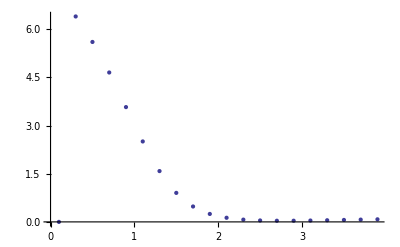

```mathematica
ListPlot[Tun2Dp20lVar]
```

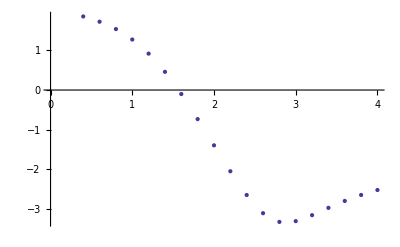

```mathematica
p18 = ListPlot[Table[{p/5.,Log[Abs[Tun2Dp20lVar[[p]][[2]] ]]},{p,2,20}]]
```

```mathematica
Tun2Dp20lVar=Tunneling2DWellListGen[20]
```

```mathematica
8/25.
```

0.32

```mathematica
TunnelingInterwellPVarp80Ext=Table[{p,computePlaneMatrix2Well[10,.5,p/2,1.+p*4.,80][[1]][[2]]-computePlaneMatrix2Well[10,.5,p/2,1.+p*4.,80][[1]][[1]]},{p,.1,10,.1}]
```

$Aborted

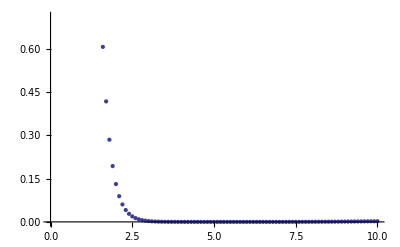

```mathematica
ListPlot[TunnelingInterwellPVarp80Ext]
```

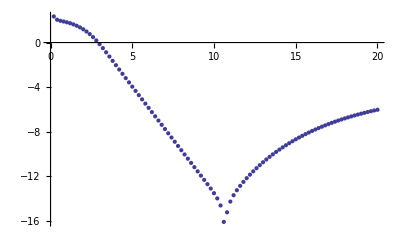

```mathematica
p18 = ListPlot[Table[{p/5.,Log[Abs[TunnelingInterwellPVarp80Ext[[p]][[2]] ]]},{p,1,100}]]
```

```mathematica
TunnelingInterwellPVarp20Ext=Table[{p,computePlaneMatrix2Well[10,.5,p/2,1.+p*4.,20][[1]][[2]]-computePlaneMatrix2Well[10,.5,p/2,1.+p*4.,20][[1]][[1]]},{p,.1,10,.1}]
```

{{0.1,10.3872},{0.2,7.7574},{0.3,7.04471},{0.4,6.60204},{0.5,6.15225},{0.6,5.65332},{0.7,5.10376},{0.8,4.51461},{0.9,3.90239},{1.,3.28657},{1.1,2.68838},{1.2,2.12954},{1.3,1.63031},{1.4,1.20643},{1.5,0.865768},{1.6,0.60633},{1.7,0.417713},{1.8,0.285292},{1.9,0.194488},{2.,0.133189},{2.1,0.0923346},{2.2,0.0655292},{2.3,0.0483819},{2.4,0.0379064},{2.5,0.0320648},{2.6,0.0294497},{2.7,0.0290729},{2.8,0.0302263},{2.9,0.0323927},{3.,0.0351875},{3.1,0.0383211},{3.2,0.0415739},{3.3,0.0447791},{3.4,0.0478111},{3.5,0.0505766},{3.6,0.0530084},{3.7,0.0550598},{3.8,0.0567013},{3.9,0.0579166},{4.,0.0587002},{4.1,0.059055},{4.2,0.0589906},{4.3,0.0585213},{4.4,0.0576653},{4.5,0.0564431},{4.6,0.0548771},{4.7,0.0529907},{4.8,0.0508078},{4.9,0.0483521},{5.,0.0456472},{5.1,0.042716},{5.2,0.0395807},{5.3,0.0362625},{5.4,0.0327816},{5.5,0.0291574},{5.6,0.0254078},{5.7,0.02155},{5.8,0.0176},{5.9,0.0135726},{6.,0.00948167},{6.1,0.00534021},{6.2,0.00116013},{6.3,0.0030475},{6.4,0.0072725},{6.5,0.0115055},{6.6,0.0157378},{6.7,0.0199616},{6.8,0.0241697},{6.9,0.0283554},{7.,0.0325128},{7.1,0.0366364},{7.2,0.0407215},{7.3,0.0447634},{7.4,0.0487584},{7.5,0.0527027},{7.6,0.0565934},{7.7,0.0604276},{7.8,0.0642029},{7.9,0.0679171},{8.,0.0715684},{8.1,0.0751553},{8.2,0.0786764},{8.3,0.0821307},{8.4,0.0855173},{8.5,0.0888355},{8.6,0.0920848},{8.7,0.0952649},{8.8,0.0983756},{8.9,0.101417},{9.,0.104389},{9.1,0.107291},{9.2,0.110125},{9.3,0.112891},{9.4,0.115588},{9.5,0.118219},{9.6,0.120782},{9.7,0.123279},{9.8,0.125712},{9.9,0.128079},{10.,0.130383}}

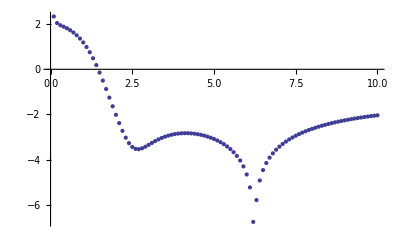

```mathematica
p18 = ListPlot[Table[{p/10.,Log[Abs[TunnelingInterwellPVarp20Ext[[p]][[2]] ]]},{p,1,100}]]
```

```mathematica
1.2/2
```

0.6

```mathematica
1+4*1.25
```

6.

```mathematica
6/20.
```

0.3

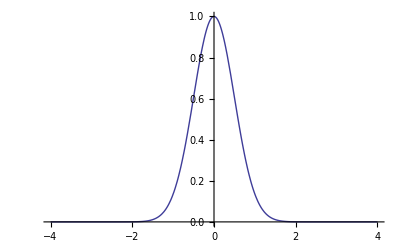

```mathematica
Plot[Exp[-2*x^2],{x,-4,4}]
```

```mathematica
TunnelingInterwellPVarp20Ext2=Table[{p,computePlaneMatrix2Well[10,.5,p/2,1.+p*5.,20][[1]][[2]]-computePlaneMatrix2Well[10,.5,p/2,1.+p*5.,20][[1]][[1]]},{p,.1,5,.1}]
```

{{0.1,9.35793},{0.2,7.42851},{0.3,6.95119},{0.4,6.56905},{0.5,6.14108},{0.6,5.64982},{0.7,5.1027},{0.8,4.51428},{0.9,3.90228},{1.,3.28653},{1.1,2.68837},{1.2,2.12954},{1.3,1.63029},{1.4,1.20631},{1.5,0.865307},{1.6,0.605053},{1.7,0.414843},{1.8,0.279782},{1.9,0.18511},{2.,0.118645},{2.1,0.0713593},{2.2,0.0369754},{2.3,0.0112888},{2.4,0.00845491},{2.5,0.0240359},{2.6,0.0365955},{2.7,0.0468634},{2.8,0.0553079},{2.9,0.0622344},{3.,0.067848},{3.1,0.0722936},{3.2,0.0756808},{3.3,0.0780989},{3.4,0.0796255},{3.5,0.0803315},{3.6,0.0802839},{3.7,0.0795468},{3.8,0.0781818},{3.9,0.0762479},{4.,0.0738019},{4.1,0.0708975},{4.2,0.0675857},{4.3,0.0639143},{4.4,0.0599281},{4.5,0.0556688},{4.6,0.051175},{4.7,0.0464824},{4.8,0.0416238},{4.9,0.0366292},{5.,0.031526}}

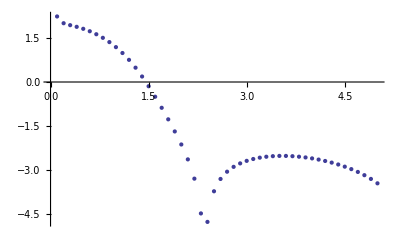

```mathematica
p19 = ListPlot[Table[{p/10.,Log[Abs[TunnelingInterwellPVarp20Ext2[[p]][[2]] ]]},{p,1,50}]]
```

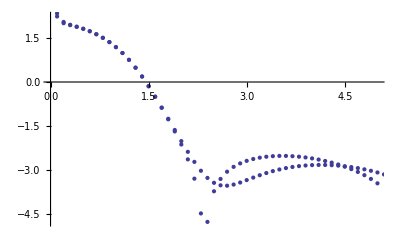

```mathematica
Show[p19,p18]
```

```mathematica
TunnelingInterwellPVarp20Ext3=Table[{p,computePlaneMatrix2Well[10,.5,p/2,7.5,20][[1]][[2]]-computePlaneMatrix2Well[10,.5,p/2,7.5,20][[1]][[1]]},{p,.1,5,.1}]
```

{{0.1,7.3017},{0.2,7.14969},{0.3,6.9008},{0.4,6.56157},{0.5,6.14096},{0.6,5.65024},{0.7,5.10281},{0.8,4.51427},{0.9,3.90233},{1.,3.28667},{1.1,2.68851},{1.2,2.12961},{1.3,1.63029},{1.4,1.20638},{1.5,0.865751},{1.6,0.606342},{1.7,0.417592},{1.8,0.284757},{1.9,0.19324},{2.,0.130964},{2.1,0.0888706},{2.2,0.0604852},{2.3,0.0412881},{2.4,0.0282001},{2.5,0.0191969},{2.6,0.0129973},{2.7,0.00878906},{2.8,0.00600658},{2.9,0.00419682},{3.,0.00298333},{3.1,0.00209439},{3.2,0.00139331},{3.3,0.000861458},{3.4,0.000530282},{3.5,0.000402391},{3.6,0.000413631},{3.7,0.000459023},{3.8,0.000459023},{3.9,0.000413631},{4.,0.000402391},{4.1,0.000530282},{4.2,0.000861458},{4.3,0.00139331},{4.4,0.00209439},{4.5,0.00298333},{4.6,0.00419682},{4.7,0.00600658},{4.8,0.00878906},{4.9,0.0129973},{5.,0.0191969}}

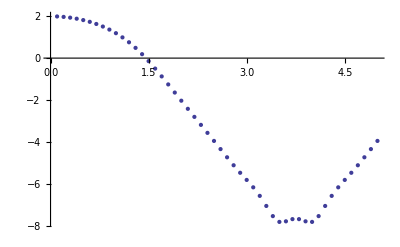

```mathematica
p20 = ListPlot[Table[{p/10.,Log[Abs[TunnelingInterwellPVarp20Ext3[[p]][[2]] ]]},{p,1,50}]]
```

```mathematica
&
```

```mathematica
WeirdVar=Table[TunnelingInterwellPVarp20Ext3=Table[{p,Log[computePlaneMatrix2Well[10,.5,p/2,7+c,20][[1]][[2]]-computePlaneMatrix2Well[10,.5,p/2,7+c,20][[1]][[1]]]},{p,.1,5,.1}],{c,.1,2,.2}];
```

```mathematica
7.3/20
```

0.365

```mathematica
h=Table[{b,Log[Exp[-2*(7+c-2.*b)^2]/Exp[-2*(2.*b)^2]]},{c,.1,2,.2},{b,.1,5,.1}];
```

```mathematica
8/20.
```

0.4

```mathematica
7.3/4*2
```

3.65

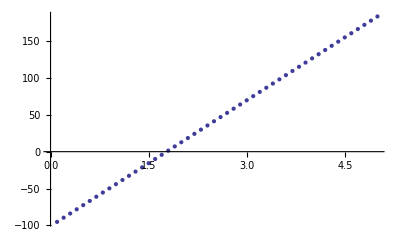
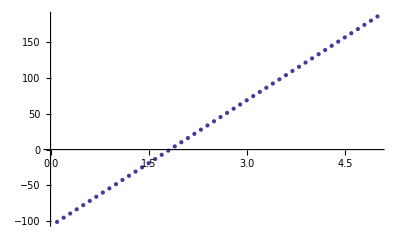
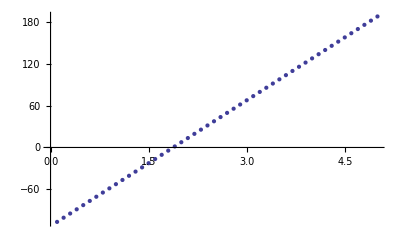
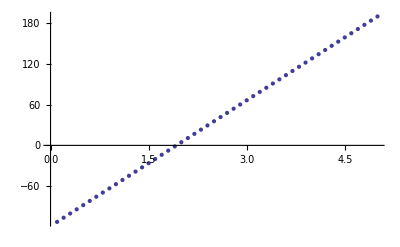
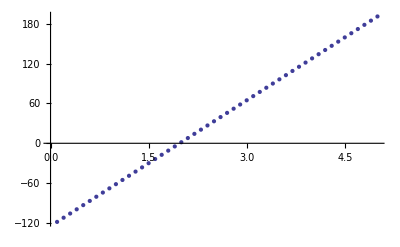
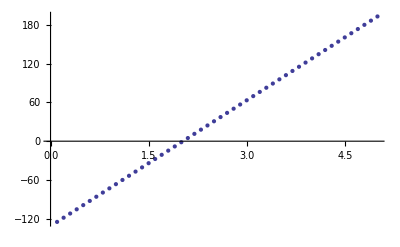
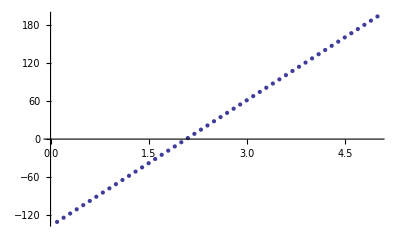
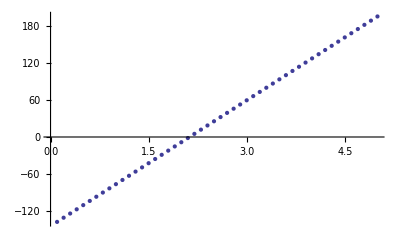

```mathematica
ListPlot/@h
```

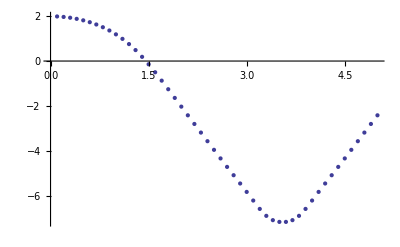
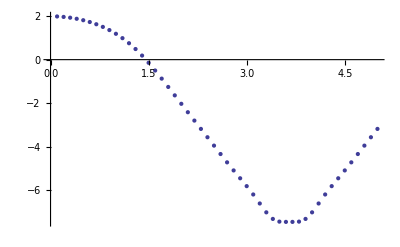
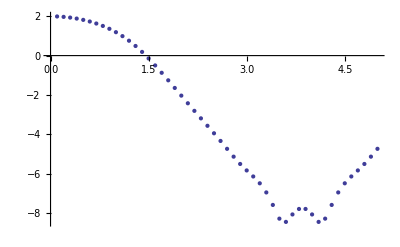
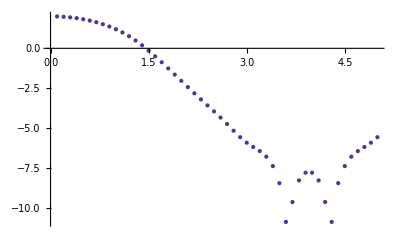
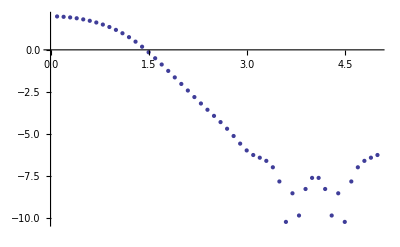
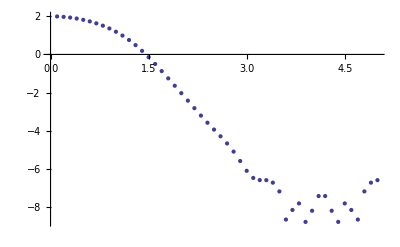
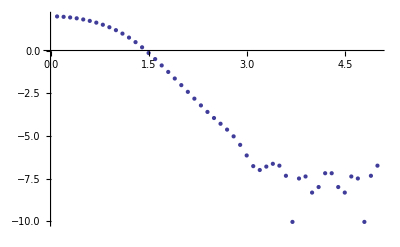
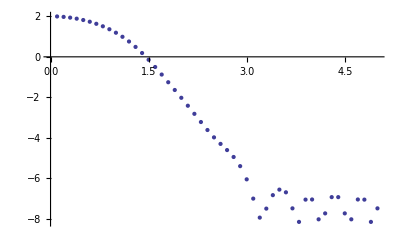
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Map[ListPlot,WeirdVar]
```

```mathematica
8.6/30
```

0.286667

```mathematica
7.3/20
```

0.365

```mathematica
WeirdVar=Table[TunnelingInterwellPVarp20Ext3=Table[{p,Log[computePlaneMatrix2Well[10,.5,p/2,8+c,30][[1]][[2]]-computePlaneMatrix2Well[10,.5,p/2,8+c,30][[1]][[1]]]},{p,2,8,.1}],{c,.1,2,.2}];
```

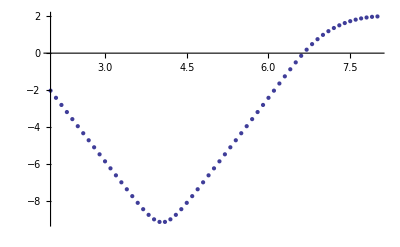
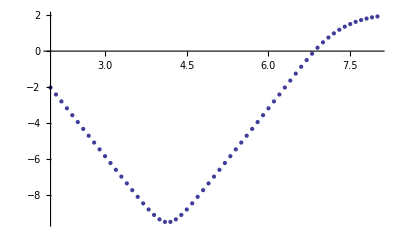
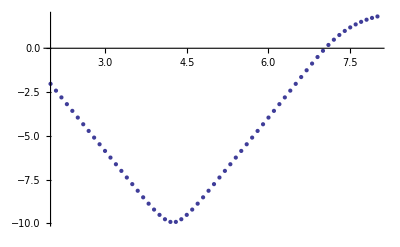
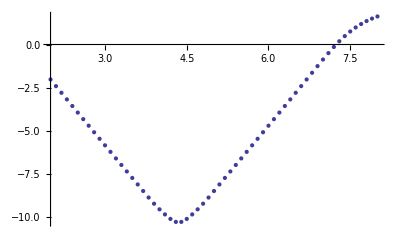
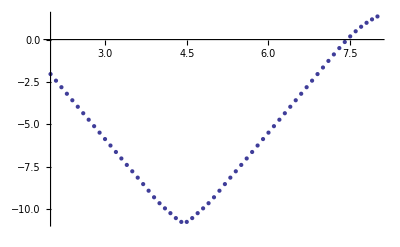
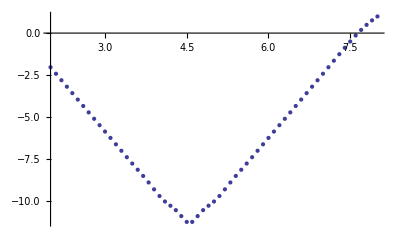
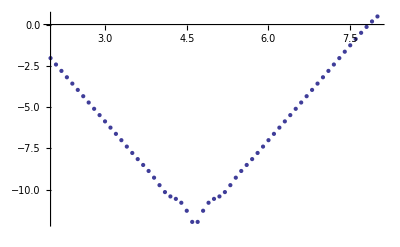
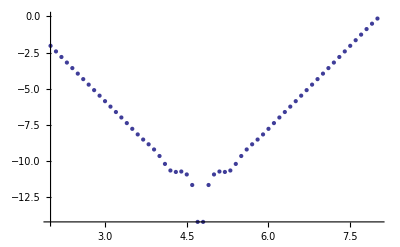

```mathematica
Map[ListPlot,WeirdVar]
```

```mathematica
WeirdVar3=Table[TunnelingInterwellPVarp20Ext3=Table[{p,Log[Abs[computePlaneMatrix2Well[10,.5,p/2,7+c,20][[1]][[1]]+10000]]},{p,.1,5,.1}],{c,.1,2,.2}];
```

```mathematica
WeirdVar3[[1]][[40]]
```

{5.9,9.41615}

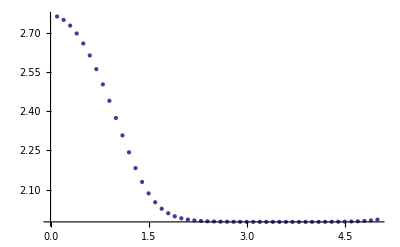
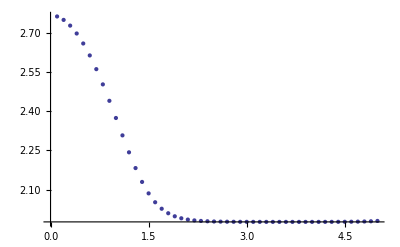
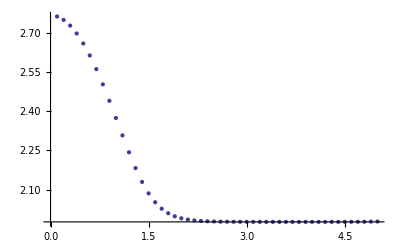
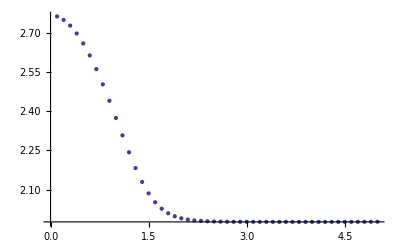
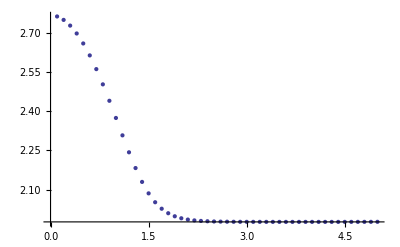
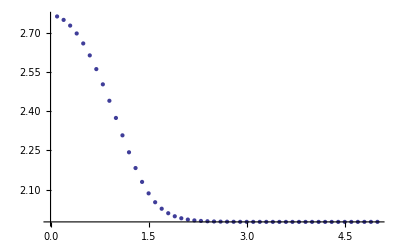
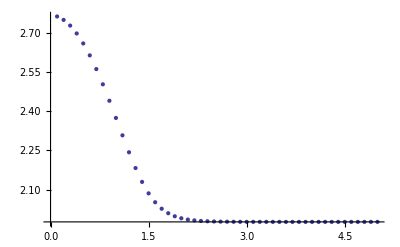
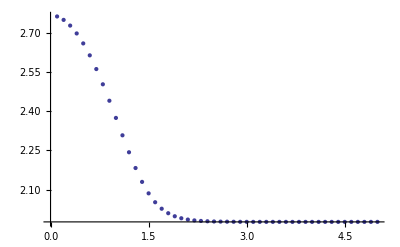

```mathematica
Map[ListPlot,WeirdVar3]
```

```mathematica
WeirdVar4=Table[TunnelingInterwellPVarp20Ext3=Table[{p,Log[Abs[computePlaneMatrix2Well[10,.5,p/2,7+c,20][[1]][[2]]+10000]]},{p,.1,5,.1}],{c,.1,2,.2}];
```

```mathematica
WeirdVar3[[1]][[40]]
```

{5.9,9.41615}

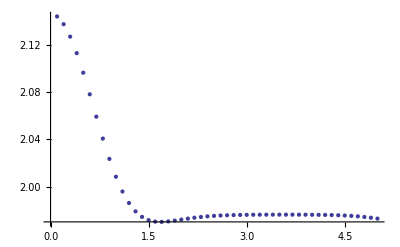
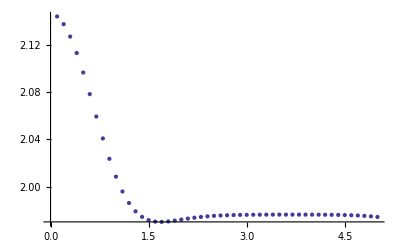
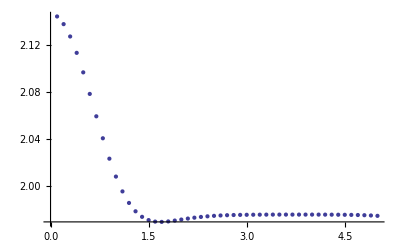
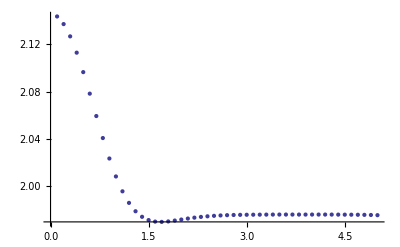
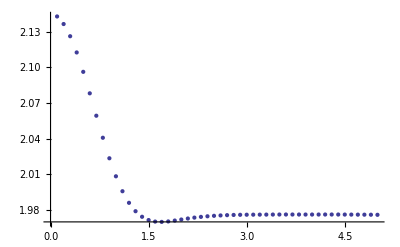
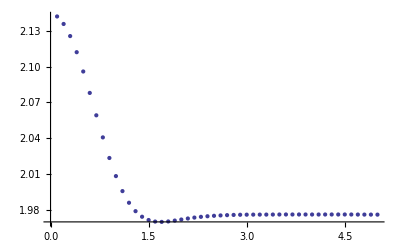
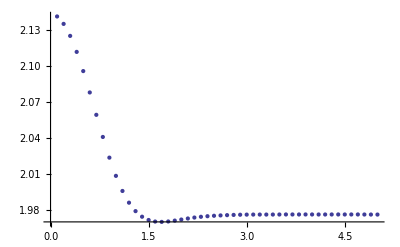
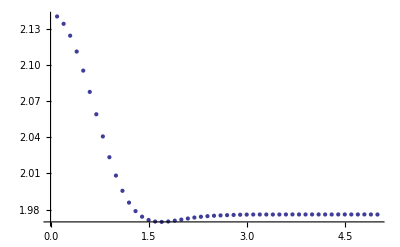

```mathematica
Map[ListPlot,WeirdVar4]
```

```mathematica
(*Let's try one more thing before home: what is the energy convergence at around 4? If it is less than 8 decimal places I think I have found my answer*)
```

```mathematica
DataConverg= Table[{Table[{p,Log10[Abs[computePlaneMatrix2Well[10,.5,b/2,7.6,p][[1]][[1]]-computePlaneMatrix2Well[10,.5,b/2,7.6,p+1][[1]][[1]]]]},{p,18,50,2}]},{b,.1,2,.5}]
```

{{{{18,-2.49956},{20,-3.0107},{22,-3.55508},{24,-4.12936},{26,-4.73071},{28,-5.35671},{30,-6.0053},{32,-6.67475},{34,-7.36387},{36,-8.06733},{38,-8.80115},{40,-9.62623},{42,-10.7402},{44,-10.8951},{46,-10.293},{48,-10.594},{50,-10.4391}}},{{{18,-3.40966},{20,-4.11613},{22,-4.87751},{24,-5.69359},{26,-6.56659},{28,-7.50217},{30,-8.52163},{32,-9.69878},{34,-10.6262},{36,-10.8951},{38,-11.1381},{40,-10.5641},{42,-10.594},{44,-11.263},{46,-10.1491},{48,Indeterminate},{50,-10.6988}}},{{{18,-4.1388},{20,-5.1847},{22,-8.2835},{24,-6.97737},{26,-7.01812},{28,-7.52671},{30,-8.27912},{32,-9.35635},{34,-10.8951},{36,-10.263},{38,-10.962},{40,-10.1067},{42,-10.536},{44,-10.4849},{46,-10.3977},{48,-10.4614},{50,-10.3977}}},{{{18,-3.44007},{20,-4.32503},{22,-6.87741},{24,-6.10358},{26,-6.19937},{28,-6.9058},{30,-9.03175},{32,-7.98997},{34,-8.00569},{36,-7.99831},{38,-7.99682},{40,-7.99525},{42,-7.99533},{44,-7.99369},{46,-7.99517},{48,-7.9933},{50,-7.99408}}}}

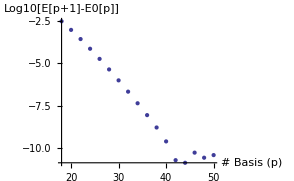
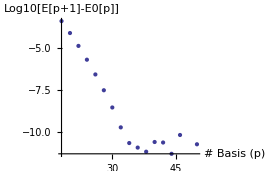
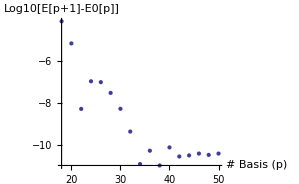
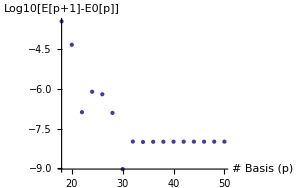

```mathematica
G1 =Map[ListPlot[#,AxesLabel->{"# Basis (p)","Log10[E[p+1]-E0[p]]"}]&,DataConverg]
```

```mathematica
(*I want to see how the 1D convergence of the energy depends on the interwell spacing. As we can see, things get fucked up. I am going to try the variable length, to see what happens*)
```

```mathematica
DataConverg= Table[{Table[{p,Log10[Abs[computePlaneMatrix2Well[10,.5,b/2,2*b+4,p][[1]][[1]]-computePlaneMatrix2Well[10,.5,b/2,2*b+4,p+1][[1]][[1]]]]},{p,18,50,2}]},{b,.1,2,.5}];
```

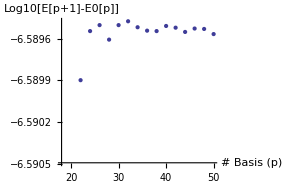
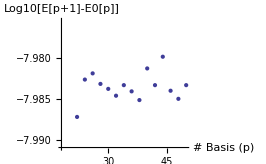
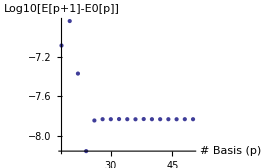
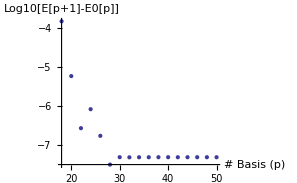

```mathematica
G1 =Map[ListPlot[#,AxesLabel->{"# Basis (p)","Log10[E[p+1]-E0[p]]"}]&,DataConverg]
```

```mathematica
DataConverg= Table[{p,Log10[Abs[computePlaneMatrix2Well[10,.5,4,7.6,p][[1]][[2]]-computePlaneMatrix2Well[10,.5,4,7.6,p+1][[1]][[2]]]]},{p,18,25,1}]
```

{{18,-2.07726},{19,-2.33719},{20,-2.60905},{21,-2.89205},{22,-3.18545},{23,-3.4886},{24,-3.8009},{25,-4.1218}}

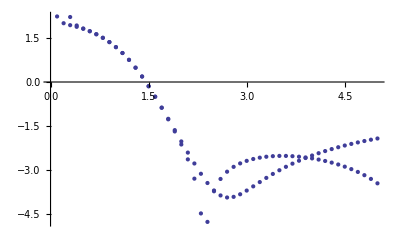

```mathematica
Show[p19,p20]
```

```mathematica
2.5/2
```

1.25

```mathematica
Exp[-2*(9-2.5)]/Exp[-2*2.5]
```

0.000335463

```mathematica
4*2.5
```

10.

```mathematica
(*Weird Summary. The convergence for p=20 and L=7 is around 10^-4, however, the shitty crap happens when the tunneling rates are around 10^-8. So we are actually doing much better than I would expect. The b will impact the convergence, probably due to the interplay with the `other' wells. Maybe I should have stayed in the Harmonic oscillator basis, this is becoming a pain. I still need a good way to quantify what is happening, and what value I can stop trusting the numerics. A numeric way to do it is calculate the convergence of the tunneling rates at a far out place, to see what L we need, and what p we need.*)
```

```mathematica
(*Tunneling rates for 2D well*)
```

```mathematica
TunnelingRatesVariableL =Table[{p,Log[computePlaneMatrix2Well[10,.5,p/2,2*p+4,20][[1]][[2]]-computePlaneMatrix2Well[10,.5,p/2,2*p+4,20][[1]][[1]]]},{p,2,8,.1}]
```

{{2.,-2.03213},{2.1,-2.42274},{2.2,-2.81626},{2.3,-3.21519},{2.4,-3.62176},{2.5,-4.03492},{2.6,-4.44378},{2.7,-4.8162},{2.8,-5.0911},{2.9,-5.20508},{3.,-5.15569},{3.1,-5.0082},{3.2,-4.83374},{3.3,-4.6754},{3.4,-4.55357},{3.5,-4.47796},{3.6,-4.45561},{3.7,-4.49615},{3.8,-4.618},{3.9,-4.86311},{4.,-5.35689},{4.1,-7.02457},{4.2,-5.61074},{4.3,-4.73294},{4.4,-4.24183},{4.5,-3.90081},{4.6,-3.64395},{4.7,-3.44315},{4.8,-3.28374},{4.9,-3.15708},{5.,-3.05774},{5.1,-2.98214},{5.2,-2.92794},{5.3,-2.89365},{5.4,-2.87851},{5.5,-2.8824},{5.6,-2.90588},{5.7,-2.95031},{5.8,-3.01814},{5.9,-3.11345},{6.,-3.24304},{6.1,-3.41875},{6.2,-3.66316},{6.3,-4.02712},{6.4,-4.67039},{6.5,-7.88482},{6.6,-4.70466},{6.7,-3.97275},{6.8,-3.54626},{6.9,-3.24443},{7.,-3.01173},{7.1,-2.8236},{7.2,-2.66692},{7.3,-2.53386},{7.4,-2.41934},{7.5,-2.31987},{7.6,-2.23295},{7.7,-2.1567},{7.8,-2.0897},{7.9,-2.03084},{8.,-1.97922}}

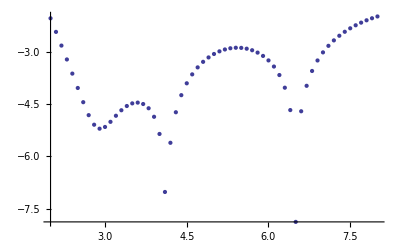

```mathematica
ListPlot[TunnelingRatesVariableL]
```

```mathematica
(*Why don't we see how this compares to the single well. We want
```

```mathematica
DataConverg= Table[{p,Log10[Abs[ComputePlaneWave[10,7.6,p+1][[1]][[1]]-ComputePlaneWave[10,7.6,p][[1]][[1]]]]},{p,18,50,2}]
```

$Aborted

```mathematica
ComputePlaneWave[10,7.6,20][[1]][[1]]
```

-10004.7

```mathematica
(*Try seeing how the energy rates converge in the ho basis to make sure things get spicy at around 10^-7
```

```mathematica
Log10[Abs[EnGround2wellHO[10,.05,.5,50][[1]]+1000-(computePlaneMatrix2Well[10,.5,.05,10,40][[1]][[1]]+10000)]]
```

-5.7723

```mathematica
computePlaneMatrix2Well[10,.5,.05,10,40][[1]][[1]]+10000
```

-15.8353

```mathematica
DataConverg2= Table[{Table[{p,Log10[Abs[computePlaneMatrix2Well[10,.5,b/2,10,p][[1]][[1]]+10000-EnGround2wellHO[10,b/2,.5,50][[1]]-1000]]},{p,18,50,2}]},{b,.1,2,.5}];
```

```mathematica
ListPlot[DataConverg2]
```

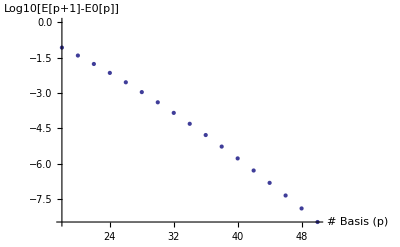
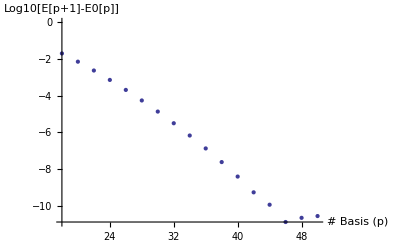
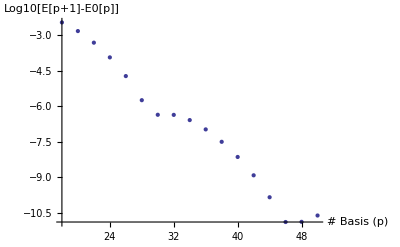
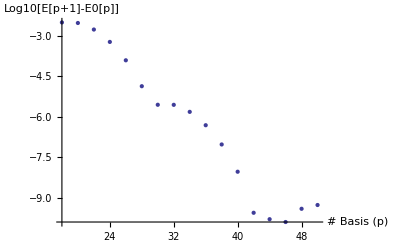

```mathematica
G2 =Map[ListPlot[#,AxesLabel->{"# Basis (p)","Log10[E[p+1]-E0[p]]"}]&,DataConverg2]
```

```mathematica
DataConverg3= Table[{Table[{p,Log10[Abs[computePlaneMatrix2Well[10,.5,b/2,4*b+5,p][[1]][[1]]+10000-EnGround2wellHO[10,b/2,.5,50][[1]]-1000]]},{p,18,50,2}]},{b,.3,8,.4}];
```

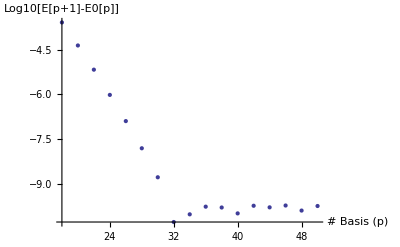
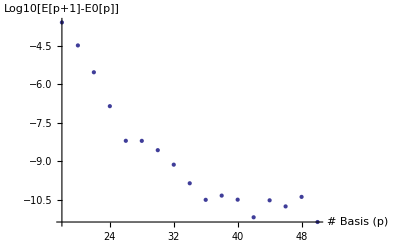
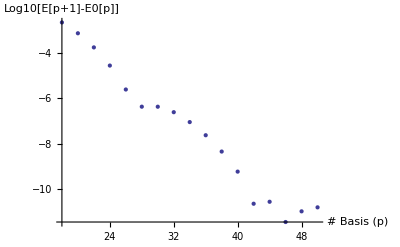
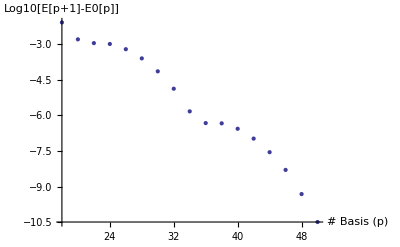
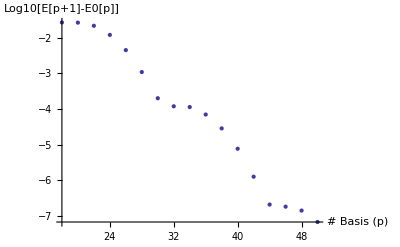
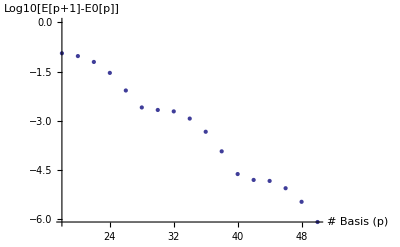
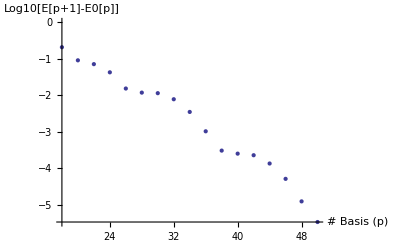
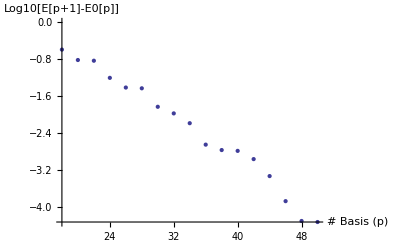

```mathematica
G2 =Map[ListPlot[#,AxesLabel->{"# Basis (p)","Log10[E[p+1]-E0[p]]"}]&,DataConverg3]
```

```mathematica
(*Let's test to make sure that the ho oscillator basis isn't just getting shitty*)
```

```mathematica
DataConvergHoBasis= Table[{Table[{p,Log10[Abs[EnGround2wellHO[10,b/2,.5,p+2][[1]]-EnGround2wellHO[10,b/2,.5,p][[1]]]]},{p,30,50,2}]},{b,3,8}];
```

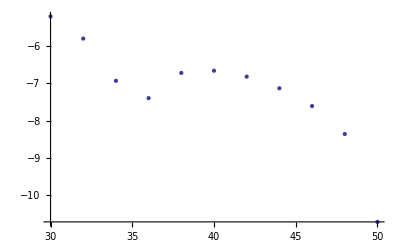
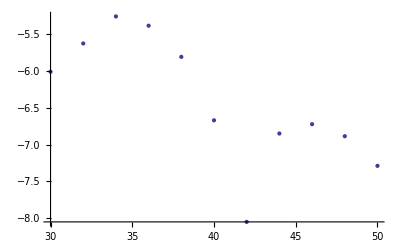
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ListPlot/@DataConvergHoBasis
```

```mathematica
(*Conclusion, things just get shitty at large interwell seperation. One last thing I can check is how well the wannier functions energy resembles the energy of a single well.
```

```mathematica
TunnelingRatesVariableL =Table[{p,Log[computePlaneMatrix2Well[10,.5,p/2,4*p+5,50][[1]][[2]]-computePlaneMatrix2Well[10,.5,p/2,4*p+5,50][[1]][[1]]]},{p,2,8,.1}]
```

{{2.,-2.03181},{2.1,-2.41934},{2.2,-2.80552},{2.3,-3.19024},{2.4,-3.57361},{2.5,-3.95585},{2.6,-4.33707},{2.7,-4.71733},{2.8,-5.09656},{2.9,-5.47479},{3.,-5.8527},{3.1,-6.23291},{3.2,-6.62264},{3.3,-7.03955},{3.4,-7.52678},{3.5,-8.21189},{3.6,-9.98267},{3.7,-8.77351},{3.8,-7.98633},{3.9,-7.57901},{4.,-7.31817},{4.1,-7.14577},{4.2,-7.04301},{4.3,-7.00729},{4.4,-7.04862},{4.5,-7.19684},{4.6,-7.53704},{4.7,-8.47057},{4.8,-8.37939},{4.9,-7.14465},{5.,-6.52252},{5.1,-6.08833},{5.2,-5.75094},{5.3,-5.47483},{5.4,-5.24224},{5.5,-5.04291},{5.6,-4.87034},{5.7,-4.72013},{5.8,-4.58913},{5.9,-4.47505},{6.,-4.37612},{6.1,-4.29104},{6.2,-4.21877},{6.3,-4.15856},{6.4,-4.10982},{6.5,-4.07219},{6.6,-4.04547},{6.7,-4.02961},{6.8,-4.02477},{6.9,-4.03133},{7.,-4.04991},{7.1,-4.08147},{7.2,-4.12743},{7.3,-4.18984},{7.4,-4.27172},{7.5,-4.37765},{7.6,-4.51481},{7.7,-4.69544},{7.8,-4.94251},{7.9,-5.30743},{8.,-5.95184}}

```mathematica
ListPlot[TunnelingRatesVariableL]
```

-Graphics-

```mathematica
(*Plots for Kaden*)
(*First, I have fixed the depth to be 10 spot sizes, to make sure that we have a second energy level. I think it might be helpful to create a manipulate figure with really crappy resolution, so we can see how the depth of the well affects the energy spacing. First, comparision of the 2D vs the 1D.*)
```

## Functions:

```mathematica
Ψ[n_,x_,m_,y_,L_]:= 1/L*Exp[-ⅈ*2 π/L(n*x+y*m)]
```

```mathematica
Hp[n_,x_,m_,y_,L_,Φ_,V_,c_,b_] := (-1/2(D[D[Φ[n,q,m,y,L],q],q]+D[D[Φ[n,x,m,w,L],w],w])-V*Exp[(-2((x-b)^2+y^2))/c^2]Φ[n,x,m,y,L])/.{q->x,w->y}
```

```mathematica
H2p[n_,x_,m_,y_,L_,Φ_,V_,c_,b_] := (-1/2(D[D[Φ[n,q,m,y,L],q],q]+D[D[Φ[n,x,m,w,L],w],w])-V*Exp[(-2((x+b)^2+y^2))/c^2]Φ[n,x,m,y,L]-V*Exp[(-2((x-b)^2+y^2))/c^2]Φ[n,x,m,y,L])/.{q->x,w->y}
```

```mathematica
HPlane[V_,L_,n_,m_,l_,q_]:= KroneckerDelta[n,l]*KroneckerDelta[m,q]*(2*π/L)^2(n^2+m^2)/2- V*Exp[(-(2*π/L)^2(n-l)^2)/8]*π*1/(2*L^2)Exp[(-(2*π/L)^2(m-q)^2)/8]
```

```mathematica
HPlanebtest[V_,L_,n_,m_,l_,q_,b_]:= 
(*I had some trouble getting the factors in EXp right, but this configuration worked. This is for one well only! This is the generalizating of HPlane, which doesn't worry about b. This basically lets me offset my one well wherever I want to double check that I have the right form of the analytics*)KroneckerDelta[n,l]*KroneckerDelta[m,q]*(2*π/L)^2(n^2+m^2)/2- V*Exp[((2b+ⅈ(2*π/L)(n-l)/2)^2-4 b^2)/2]*π*1/(2*L^2)Exp[(ⅈ(2*π/L)(m-q))^2/8]
```

```mathematica
H2Plane[V_,L_,b_,n_,m_,l_,q_]:= KroneckerDelta[n,l]*KroneckerDelta[m,q]*(2*π/L)^2(n^2+m^2)/2- V*Exp[((2b+ⅈ(2*π/L)(n-l)/2)^2-4 b^2)/2]*π*1/(2*L^2)Exp[(ⅈ*(2*π/L)(m-q))^2/8]-V*Exp[((-2b+ⅈ(2*π/L)(n-l)/2)^2-4 b^2)/2]*π*1/(2*L^2)Exp[(ⅈ*(2*π/L)(m-q))^2/8]//N
```

```mathematica
HMatrix[V_,L_,size_]:=ArrayFlatten[Table[HPlane[V,L,m,l,n,q],{m,-size,size},{n,-size,size},{l,-size,size},{q,-size,size}]//N]
```

```mathematica
groundState[EM_,L_,x_,y_]:=Compile[{Size=Sqrt[Length[EM]], i,j},
(*Given an eigenvector, this will compute a plottable version of the wavefunction. However, there is little sophistication, the user must still change the index conversion number by hand.

Note: there was a problem: use ky for calculating the number on x and y, as the kx function gives the row of a matrix, but, for the eigenvector, it is just a 'column' vector, so just use ky*) Sum[Normalize[EM][[(i-1)*Size+j]]*N[Exp[-ⅈ*2.*π/L*(ky[i,Size]*x+ky[j,Size]*y)]/L,8],{i,1,Size},{j,1,Size}]]
```

```mathematica
GroundStatePlane[p_,l_]:= Module[{HMatrix,EN,G,m,k,n,q},
HMatrix=Table[HPlane[1.5,10,m,l,n,q],{m,-p,p},{n,-p,p},{k,-p,p},{q,-p,p}];
EN = Eigensystem[ArrayFlatten[HMatrix]-100*IdentityMatrix[(2*p+1)^2]];
G = {EN[[1]][[1]]+100,EN[[2]][[1]]}]
```

```mathematica
GroundStatePlane[p_,l_]:= Module[{HMatrix,EN,G,m,k,n,q},
HMatrix=Table[HPlane[1.5,10,m,l,n,q],{m,-p,p},{n,-p,p},{k,-p,p},{q,-p,p}];
EN = Eigensystem[ArrayFlatten[HMatrix//N]-100*IdentityMatrix[(2*p+1)^2]];
G = {EN[[1]][[1]]+100,EN[[2]][[1]]}]
```

Harmonic Oscillator Functions:
HMV1[1,2,.1,0,.5]

```mathematica
HMV1[1,1,.1,0,0.5]
```

0.0103913

```mathematica
HMV1[1,2,0.1,0.5]
```

HMV1[1,2,0.1,0.5]

```mathematica
HMV1[l_,m_,ω_,b_,c_]:= (Sqrt[ω]/Sqrt[2^(l+m)Factorial[l]*Factorial[m]]*Sum[{2^k Factorial[k]*Binomial[l,k]*Binomial[m,k]*(1-2*(ω*c^2)/(1+2 c^2 ω))^((m+l)/2-k)*HermiteH[(m+l-2*k),Sqrt[ω/(1+2*c^2*ω)]*b]},{k,0,Min[m,l]}]*Exp[b^2/(2 c^2)(1/(1+2 c^2*ω)-1)]*Sqrt[2/(1+2 c^2*ω)]c)[[1]]
```

```mathematica
Hx2Anal2[l_,m_]:= 1/2(2*l+1)*KroneckerDelta[l,m]-1/2 Sqrt[(l+1)(l+2)]KroneckerDelta[l+1,m-1]-1/2 Sqrt[(m+1)(m+2)]KroneckerDelta[l-1,m+1]
```

```mathematica
HOBasis[V_,b_,c_,size_]:= Module[{ω=Sqrt[(2V)/c^2]},Table[ω/2*Hx2Anal2[n,m]+ω/2*Hx2Anal2[l,q]-V*HMV1[n,m,ω,b,c]*HMV1[l,q,ω,0,c],{n,0,size-1},{l,0,size-1},{m,0,size-1},{q,0,size-1}]]
```

```mathematica
HOBasis1Well[V_,c_,size_]:= Module[{ω=Sqrt[2*V/c^2]},Table[ω/2*Hx2Anal2[n,m]*KroneckerDelta[l,q]+ω/2*Hx2Anal2[l,q]*KroneckerDelta[m,n]-V*HMV1[n,m,ω,0,c]*HMV1[l,q,ω,0,c],{n,0,size-1},{m,0,size-1},{l,0,size-1},{q,0,size-1}]]
```

```mathematica
plotGround[Ψ_,H_,V_,c_,b_,size_,]:= Compile[{x,k,Em,M,HOBasis},

Plot[{Sum[k,{k,Table[Ψ[n,x,V,c]*Normalize[Em[[2]][[1]]][[n+1]], {n,0,size}]}],-V/(c*Sqrt[2π])Exp[-x^2/(4.*V*c^2)]//N},{x,-10,10}]
]
```

```mathematica
plotGround
```

plotGround

```mathematica
plotGround2wellHO2d[Ψ_,V_,b_,c_,size_]:= Module[{k,ω=Sqrt[2*V/(6b*c+9 c^2)],HOBasis,Em},
HOBasis[V,b,c,size,ω]:= Module[{},Table[ω/2*Hx2Anal2[n,m]+ω/2*Hx2Anal2[l,q]-V*HMV1[n,m,ω,-b,c]*HMV1[l,q,ω,b,c],{n,0,size},{l,0,size},{m,0,size},{q,0,size}]];
Em = Eigensystem[ArrayFlatten[HOBasis[1.5^2,1,.5,7,ω]-1000*IdentityMatrix[42]]]

Plot[{Abs[Sum[Ψ[i-1,x,V,c,ω]*Ψ[j-1,x,V,c,ω]*Normalize[Em[[2]][[1]]][[(i-1)*(size)+j]],{i,1,17},{j,1,17}]]^2},{x,-3,3}]
]
```

```mathematica
plotGround2wellHO2dT[Ψ_,V_,b_,c_,size_,Em_]:= Module[{k,ω=Sqrt[2*V/c^2],x,y},
Sum[Ψ[i-1,x,V,c,ω]*Ψ[j-1,y,V,c,ω]*Normalize[Em[[2]][[1]]][[(i-1)*(size)+j]],{i,1,size},{j,1,size}];

Plot3D[{Abs[Sum[Ψ[i-1,x,V,c,ω]*Ψ[j-1,y,V,c,ω]*Normalize[Em[[2]][[1]]][[(i-1)*(size)+j]],{i,1,size},{j,1,size}]]^2},{x,-3,3},{y,-3,3}]
]
```

```mathematica
HM2Well[V_,b_,c_,size_]:= Module[{ω=Sqrt[2*V/(6*b*c+9 c^2)]},
Table[ω/2*Hx2Anal2[n,m]-V*HMV1[n,m,ω,b,c]-V*HMV1[n,m,ω,-b,c],{n,0,size},{m,0,size}]
]
```

```mathematica
EnGround2wellHO[V_,b_,c_,size_]:=EnGround2wellHO[V,b,c,size]= Module[{Em,M},

(M=HM2Well[V,b,c,size]-1000*IdentityMatrix[size+1]);
(Em=Eigenvalues[M])
]
```

### Sparse Matrices Stuff:

```mathematica
R[deltaK_,L_]:=R[deltaK]=Exp[(-(2*π/L)^2(deltaK)^2)/8.]//N
```

```mathematica
yIndex[i_,size_] =Mod[i,size,1]
```

Mod[i,size,1]

```mathematica
(*y index will take a number from 1-n, and convert it into a quantum number for ky. This will be an integer starting from -p..p.*)
```

```mathematica
yIndex[2,4]
```

2

```mathematica
ky[i_,size_]=yIndex[i,size]-(size-1)/2-1
```

-1+(1-size)/2+Mod[i,size,1]

```mathematica
(*this will convert our index number to a range that runs over negative numbers so we can get backwards waves*)
```

```mathematica
kx[i_,size_]=xIndex[i,size]-(size-1)/2-1
```

(1-size)/2+(i-Mod[i,size,1])/size

```mathematica
kx[6,5]
```

-1

```mathematica
xIndex[i_,size_]=(i-Mod[i,size,1])/size+1
```

1+(i-Mod[i,size,1])/size

```mathematica
BuildPlaneMatrix[V_,L_,p_]:= Module[{MDense,MDiag,i,j,M},

MDense = -V*π*1/(2*L^2)*SparseArray[{i_,j_}->R[kx[j,p]-kx[i,p],L]*R[ky[j,p]-ky[i,p],L],{p^2,p^2},0];
MDiag =SparseArray[{i_,i_}->(2*π/L)^2((kx[i,p])^2+(ky[i,p])^2)/2,{p^2,p^2},0];
M = MDense+MDiag
]
```

```mathematica
Clear[R]
```

```mathematica
1/Sqrt[2]//N
```

0.707107

```mathematica
BuildPlaneMatrix2D2Well[V_,L_,p_,b_]:= Module[{MDense,MDiag,i,j,M},
(* I am choosing the wells to be on the x-axis, so the y-axis dynamics shouldn't
change. Notice, the R2W contains b information, and will be used for the kx's, while the R doesn't, and can be used for the ky's without loss of generality, because there are two wells, there is another term in our MDense*)
MDense = -V*π*1/(2*L^2)*SparseArray[{i_,j_}->(R2W[kx[j,p]-kx[i,p],L,b]+R2W[kx[j,p]-kx[i,p],L,-b])*R[ky[j,p]-ky[i,p],L],{p^2,p^2},0];
MDiag =SparseArray[{i_,i_}->(2*π/L)^2((kx[i,p])^2+(ky[i,p])^2)/2,{p^2,p^2},0];
M = MDense+MDiag
]
```

```mathematica
R2W[deltaK_,L_,b_]:=R2W[deltaK,L,b]=Exp[((2.*b+ⅈ(2.*π/L)(deltaK)/2)^2-4.*b^2)/2.]//N
```

```mathematica
(*Tunneling for a 2D 2Well case*)
Tunneling2DWellListGen[basisnum_]:=
(*Need to double check that L=1 is okay for small b*)Module[{EnergyList,TunnelingList},
EnergyList= Table[{b,Eigenvalues[BuildPlaneMatrix2D2Well[10,8,basisnum,b/2.]-1000.*IdentityMatrix[basisnum^2],2]+1000},{b,.1,4,.2}];

TunnelingList= Table[{EnergyList[[p]][[1]],EnergyList[[p]][[2]][[2]]-EnergyList[[p]][[2]][[1]]},{p,1,Length[EnergyList]}]
]
```

```mathematica
10/25.
```

0.4

```mathematica
(*1D Functions for plane waves*)
```

```mathematica
computePlaneMatrix2Well[V_,c_,b_,length_,p_]:= Module[{l,m,H,Em,M,norm},
(*First normalize the plane wave on the length*)
H[l_,m_]:=m^2/2 KroneckerDelta[m,l] - V*Exp[1/(2 c^2)(-b+ⅈ*c^2(l-m))^2-b^2/(2 c^2)]*Sqrt[π]*(Sqrt[2]c)/length-V*Exp[(1/(2 c^2)(b+ⅈ*c^2(l-m))^2-b^2/(2 c^2))]*Sqrt[π]*(Sqrt[2]c)/length;
M = Eigensystem[Table[H[2π*l/length,2π*m/length],{l,-p/2.,p/2},{m,-p/2.,p/2.}]-10000*IdentityMatrix[p+1],3]

]
```

```mathematica
ComputePlaneWave[V_,L_,p_]:= Module[{MDense,MDiag,i,j,M,EM},

MDense = -V*π*1/(2*L^2)*SparseArray[{i_,j_}->R[kx[j,p]-kx[i,p],L]*R[ky[j,p]-ky[i,p],L],{p^2,p^2},0];
MDiag =SparseArray[{i_,i_}->(2*π/L)^2((kx[i,p])^2+(ky[i,p])^2)/2,{p^2,p^2},0];
M = MDense+MDiag;

EM = Eigensystem[M-10000*IdentityMatrix[p^2],3]
]
```